# Equivariant Polynomial Tensor Functions

Michael Liu

## Abstract

We present an algorithm to compute a vector space basis for the space M:=Hom_G(𝒮(X),Y) of harmonic-tensor-valued SO(3)-equivariant polynomial functions with arbitrary harmonic-tensor inputs. This algorithm relies on Schur-Weyl duality, the Clebsch-Gordan theory of SO(3), and the explicit plethysm problem for the symmetric power 𝒮^D(X) of a finite dimensional SO(3)-representation X.

We present an algorithm to compute an algebra basis for the algebra R:=Hom_G(𝒮(X),ℝ), and we present a closely related algorithm to compute a module basis for the R-module M when Y is an irreducible representation of SO(3). These algorithms sub-select from the above vector space basis using Nakayama’s lemma.

## Notation

G:=SO(3)

Λ:=ℕ_0, λ,μ,ν∈Λ

H_λ:=𝒮^λ(ℂ^3)∩ker tr the irreducible representation of G of dimension 2λ+1

X:= any finite dimensional representation of G

Y:= any irreducible representation of G

Hom_G(X,Y):= the space of G-equivariant linear maps from X to Y

## Problem Statement

#### Definition

Let

R:=(𝒮(X^*))^G≅Hom_G(𝒮(X),ℝ)

be the set of invariant polynomial functions from X to ℝ, and let

M:=(𝒮(X^*)⊗Y)^G≅Hom_G(𝒮(X),Y)

be the set of equivariant polynomial functions from X to Y.

#### Problem

Find bases for R as an ℝ-algebra and M as an R-module.

## Nakayama’s Lemma

#### Lemma (Nakayama)

Let M=⊕_(D∈ℕ_0)M^D be a finitely generated graded module over a graded ring R=⊕_(D∈ℕ_0)R^D, where R_0=ℝ. Let I:=⊕_(D∈ℕ)R^D be the ideal generated by the positively graded elements of R. Let L⊆M. Then L/I M generates M/I M as an ℝ-module iff L generates M as an R-module.

#### Algorithm

Suppose that we are given bases ℛ_D,ℳ_D for R^D,M^D as ℝ-modules. Note that

(I M)^D:=I M∩M^D=∑_(1<=D'<=D) R_D' M_(D-D'),
I M=⊕_(D∈ℕ)(I M)^D,
M/I M≅⊕_(D∈ℕ)M^D/(I M)^D.

Moreover,

(I M)^D=Span{r_D' m_(D-D')|1<=D'<=D,r_D'∈ℛ_D',m_(D-D')∈ℳ_(D-D')}.

Now, define

D_max:=max{D∈ℕ|M^D/(I M)^D!=0},

We have a Hilbert series for M_D, we need one for (I M)_D to get these degrees.

which may be difficult to determine in practice. For each 1<=D<=D_max, compute a basis for (I M)_D and extend it to a basis for M^D by adjoining the basis vectors in the set L_D⊆M^D. Write L:=∪_(D∈ℕ)L_D. Since L_D/(I M)_D is a basis for M^D/(I M)_D, L/I M is a basis for M/I M, so by Nakayama’s Lemma, L is a minimal generating set for M as an R-module.

Next, apply the above algorithm with M=I. Let ℝ[L] be the ℝ-algebra generated by L. Clearly, ℝ⊆ℝ[L]. Now, write R_(<=D):=R_0⊕…⊕R^D, and suppose that R_(<=D)⊆ℝ[L]. Then

R_(D+1)=I_(D+1)⊆Span_ℝ(L_(D+1))+(I^2)_(D+1)=Span_ℝ(L_(D+1))+∑_(1<=D'<=D) I_D' I_(D+1-D').

Clearly, Span_ℝ(L_(D+1))⊆ℝ[L], and by the inductive hypothesis, I_1,...,I_D⊆R_(<=D)⊆ℝ[L]. Thus, R=ℝ[L]. To see that L is minimal, note that if any L⊆I generates R as an ℝ-algebra, then L generates I as an R-module, so L/I^2 generates I/I^2 as an ℝ-module. Thus, since our given L makes L/I^2 a basis for I/I^2, our given L is a minimal generating set for R as an ℝ-algebra.

#### Problem

Find bases for R^D,M^D as vector spaces.

## Isotypic Decomposition

#### Algorithm

Let

X=⊕_λ H_λ⊗M_λ.

Then 𝒮^D(X^*) has some isotypic decomposition

𝒮^D(X^*)≅⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,𝒮^D(X^*)).

Suppose that we are given bases for the multiplicity spaces Hom_G(H_ν,𝒮^D(X^*)) as well as the explicit isomorphism embedding each isotypic component H_ν⊗Hom_G(H_ν,𝒮^D(X^*)) into 𝒮^D(X^*). Let Y=H_ρ. Then

R^D≅H_0⊗Hom_G(H_0,𝒮^D(X^*)),
M^D≅(H_ρ⊗H_ρ)^G⊗Hom_G(H_ρ,𝒮^D(X^*)).

Thus, a basis for R^D is given by the isotypic basis vectors in 𝒮^D(X^*) corresponding to the 0-isotypic component H_0⊗N_0^D. Moreover, a basis for M^D is given as follows. First, apply the Clebsch-Gordan isomorphism H_0->(H_ρ⊗H_ρ)^G to obtain the unique G-invariant vector v in H_ρ⊗H_ρ. For each basis vector m in N_ρ^D, send v⊗m through the isomorphism above to obtain basis vectors in 𝒮^D(X^*) corresponding to M^D.

#### Problem

Find bases for Hom_G(H_0,𝒮^D(X^*)) and Hom_G(H_ρ,𝒮^D(X^*)) as vector spaces.

## Explicit Isotypic Decomposition of the Symmetric Power 𝒮^D(X)

#### Remark

Recall that 𝒮^D(X) has the isotypic decomposition

𝒮^D(X)≅⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,𝒮^D(X)).

Our goal in this section is to obtain an explicit expression for Hom_G(H_ν,𝒮^D(X)). All isomorphisms below are isomorphisms of G-modules.

#### Theorem (Isotypic Decomposition of 𝒮^D(X))

Let ν,D∈ℕ_0, and let X=⊕_λ H_λ⊗M_λ be finite dimensional. For any partition π, let e_π denote any corresponding Young symmetrizer. Then

Hom_G(H_ν,𝒮^D(X))≅⊕_((d_λ)_λ)⊕_((π_λ)_λ)⊕_((μ_λ)_λ)Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ))),

where the sums are over all sequences (d_λ)_λ of nonnegative integers such that ∑_λ d_λ=D, all sequences (π_λ)_λ of integer partitions such that each π_λ⊢d_λ has largest part at most min(dim H_λ,dim M_λ), and all sequences (μ_λ)_λ of nonnegative integers such that each H_μ_λ appears in e_π_λ(H_λ^(⊗d_λ)) and H_ν appears in ⊗_λ H_μ_λ.

#### Proof

We have

𝒮^D(X)≅𝒮^D(⊕_λ H_λ⊗M_λ)≅^Sym⊕_((d_λ)_λ)⊗_λ 𝒮^d_λ(H_λ⊗M_λ)≅^(rearrange ⊗, Sym)⊕_((d_λ)_λ)⊗_λ⊕_π_λ e_π_λ(H_λ^(⊗d_λ))⊗e_π_λ(M_λ^(⊗d_λ))≅^(rearrange ⊗)⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ))),

where the third isomorphism is due to the Cauchy decomposition, which follows from Schur-Weyl duality. Now, decompose each e_π_λ(H_λ^(⊗d_λ)) to obtain

⊗_λ e_π_λ(H_λ^(⊗d_λ))≅^(apply Hom)⊗_λ⊕_μ_λ H_μ_λ⊗Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))≅^(rearrange ⊗)⊕_((μ_λ)_λ)(⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))).

Finally, Clebsch-Gordan yields

⊗_λ H_μ_λ≅^(apply Hom)⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ).

#### Remark

To speed up our algorithm, we obtain an explicit expression for Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))).

#### Theorem (Isotypic Decomposition of e_π_λ(H_λ^(⊗d_λ)))

Let λ,d_λ,μ_λ∈ℕ_0, and let π_λ=(π_(λ,p))_p be a partition of d_λ. Then

Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))≅r_π_λ(⊕_((ξ_(λ,p))_p)Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p)))⊗(⊗_p Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))),

where the sum is over all sequences (ξ_(λ,p))_p of nonnegative integers such that each H_(ξ_(λ,p)) appears in Λ^(π_(λ,p))(H_λ) and H_μ_λ appears in ⊗_p H_(ξ_(λ,p)).

#### Proof

We have

e_π_λ(H_λ^(⊗d_λ))≅r_π_λ(c_π_λ(H_λ^(⊗d_λ)))≅r_π_λ(⊗_p Λ^(π_(λ,p))(H_λ))≅^(apply Hom)r_π_λ(⊗_p⊕_(ξ_(λ,p))H_(ξ_(λ,p))⊗Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))≅^(rearrange ⊗)r_π_λ(⊕_((ξ_(λ,p))_p)(⊗_p H_(ξ_(λ,p)))⊗(⊗_p Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))).

Clebsch-Gordan yields

⊗_p H_(ξ_(λ,p))≅^(apply Hom)⊕_μ_λ H_μ_λ⊗Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p))).

Thus,

e_π_λ(H_λ^(⊗d_λ))≅^(rearrange ⊗)r_π_λ(⊕_μ_λ H_μ_λ⊗⊕_((ξ_(λ,p))_p)Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p)))⊗(⊗_p Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ))))≅⊕_μ_λ H_μ_λ⊗r_π_λ(⊕_((ξ_(λ,p))_p)Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p)))⊗(⊗_p Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))),

where the last isomorphism holds since r_π_λ is G-equivariant.

## Algorithm: Basis for an Isotypic Component of the Symmetric Power 𝒮^D(X)

Fix X=⊕_λ H_λ⊗M_λ.

#### Overview: Grow Tree

Given ν,D∈ℕ_0

set D as the root of a tree

for each leaf D

for each (d_λ∈ℕ_0)_λ with ∑_λ d_λ=D

spawn a new leaf containing (d_λ)_λ

for each leaf (d_λ)_λ

for each (π_λ⊢d_λ)_λ with all π_(λ,1)<=min{dim H_λ,dim M_λ}

spawn a new leaf containing (π_λ)_λ

for each leaf (π_λ)_λ

for each (μ_λ∈ℕ_0)_λ with each H_μ_λ appearing in e_π_λ(H_λ^(⊗d_λ)) and H_ν appearing in ⊗_λ H_μ_λ

spawn a new leaf containing (μ_λ)_λ

for each leaf (μ_λ)_λ

compute path bases for Hom_G(H_ν,⊗_λ H_μ_λ) and for each Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))

for each node (π_λ)_λ

compute SSYT bases for each e_π_λ(M_λ^(⊗d_λ))

#### Overview: Harvest Tree

Given a tree from above

for each path from root to leaf

compute tensor bases for Hom_G(H_ν,⊗_λ H_μ_λ), for each Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))), and for each e_π_λ(M_λ^(⊗d_λ))

take Tuples and contract to compute a tensor basis for Hom_G(H_ν,⊗_λ e_π_λ(H_λ^(⊗d_λ)))

#### Optimizations

D,d_λ<=D,π_(,λ,p)<=D,μ_λ<=(max Λ_X)D,γ<=|Λ_X|(max Λ_X)D: 8-bit unsigned integer (0,...,255)
⊗_p CG(γ_(λ,p)): SymmetrizedArray with direct coefficient computation

For Hom_G(H_ν,⊗_λ⊗_p H_(μ_(λ,p))) that are absolutely necessary to compute, compute via tensor train, memoize Clebsch Gordan tensors
For Hom_G(H_(μ_(λ,p)),Λ^(π_(λ,p))(H_λ)), use antisymmetrized components

## Algorithm: Basis for an Isotypic Component of 𝒮^D(X)⊗Y

#### Overview

Run previous algorithm to obtain maps

Single CG step

Combine maps

## Code

### General Functions

#### Compute Isotypic Multiplicities

```mathematica
ClearAll[
SchurS,
IsotypicComponentTensorProductQ,
IsotypicMultiplicityAntisymmetricPower,
IsotypicMultiplicitySchurPower
]
```

```mathematica
SchurS=ResourceFunction["SchurS"];
```

```mathematica
IsotypicComponentTensorProductQ[λs_,μ_]:=With[{m=Max[λs],s=Total[λs]},Max[0,2m-s]<=μ<=s]
```

```mathematica
IsotypicMultiplicityAntisymmetricPower[λ_,d_,μ_]:=Count[#,_?(Total[#]==μ&)]-Count[#,_?(Total[#]==μ+1&)]&@Subsets[Range[-λ,λ],{d}]
```

```mathematica
IsotypicMultiplicitySchurPower[λ_,p_,μ_]:=
Which[
p=={0}∧μ==0,1,
p=={0}∧μ!=0,0,
True,Module[{x},Coefficient[#,x,μ]-Coefficient[#,x,μ+1]&@SchurS[p,x^Range[-λ,λ]]]
]
```

#### Enumerate Isotypic Components

```mathematica
ClearAll[
IsotypicComponentsTensorProduct,
IsotypicComponentsTensorPower,
IsotypicComponentsAntisymmetricPower,
IsotypicComponentsSchurPower
]
```

```mathematica
SetAttributes[
{
IsotypicComponentsTensorProduct,
IsotypicComponentsTensorPower,
IsotypicComponentsAntisymmetricPower
},
Listable
]
```

```mathematica
IsotypicComponentsTensorProduct[a_,b_]:=Range[Abs[a-b],a+b]
```

```mathematica
IsotypicComponentsTensorPower[λ_,d_]:=If[d==1,{λ},Range[0,λ d]]
```

```mathematica
IsotypicComponentsAntisymmetricPower[λ_,d_]:=
Select[
IsotypicComponentsTensorPower[λ,d],
IsotypicMultiplicityAntisymmetricPower[λ,d,#]>0&
]
```

```mathematica
IsotypicComponentsSchurPower[λ_,p_]:=
Select[
IsotypicComponentsTensorPower[λ,Total[p]],
IsotypicMultiplicitySchurPower[λ,p,#]>0&
]
```

#### Clebsch-Gordan Tensors

```mathematica
ClearAll[
MemoizedClebschGordanCoefficient,
FullClebschGordanCoefficient,
AntisymmetrizedClebschGordanTensor,
MemoizedClebschGordanTensor,
FullClebschGordanTensor,
tensorMultiply,
changeBasis
]
```

```mathematica
MemoizedClebschGordanCoefficient[λ1_,m1_,λ2_,m2_,λ3_,m3_]:=MemoizedClebschGordanCoefficient[λ1,m1,λ2,m2,λ3,m3]=
N[ClebschGordan[{λ1,m1},{λ2,m2},{λ3,m3}]]
```

```mathematica
FullClebschGordanCoefficient[γs_,ms_]:=
With[
{ss=Accumulate[ms]},
Times@@MapThread[MemoizedClebschGordanCoefficient,{Most[γs],Most[ss],ConstantArray[First[γs],Length[γs]-1],Rest[ms],Rest[γs],Rest[ss]}]
]
```

```mathematica
AntisymmetrizedClebschGordanTensor[γs_]:=
If[
Length[γs]==1,
1,
Module[
{λ=First[γs],μ=Last[γs],d=Length[γs],msList,λsμ},

(*We could still try to generate these directly somehow...*)
msList=Select[Permutations[Range[-λ,λ],{d}],-γs\[VectorLessEqual]Accumulate[#]\[VectorLessEqual]γs&];
λsμ=Append[ConstantArray[λ,d],μ];

Chop@Symmetrize[
SymmetrizedArray[
1+λsμ+Append[#,Total[#]]->FullClebschGordanCoefficient[γs,#]&/@msList,
2λsμ+1
],
Antisymmetric[Range[d]]
]
]
]
```

```mathematica
MemoizedClebschGordanTensor[λ1_,λ2_,λ3_]:=MemoizedClebschGordanTensor[λ1,λ2,λ3]=
Chop@SparseArray[
Join@@Table[
{1+λ1+m1,1+λ2+m2,1+λ3+m1+m2}->MemoizedClebschGordanCoefficient[λ1,m1,λ2,m2,λ3,m1+m2],
{m1,-λ1,λ1},{m2,Max[-λ2,-λ3-m1],Min[λ2,λ3-m1]}
],
{2λ1+1,2λ2+1,2λ3+1}
]
```

```mathematica
FullClebschGordanTensor[λs_,γs_]/;
First[λs]==First[γs]∧
Length[λs]>=1∧
Length[λs]==Length[γs]∧
Abs[ListConvolve[{1,-1},γs]]\[VectorLessEqual]Rest[λs]\[VectorLessEqual]ListConvolve[{1,1},γs]:=
If[
Length[λs]==1,
1,
Chop@Dot@@MapThread[MemoizedClebschGordanTensor,{Most[γs],Rest[λs],Rest[γs]}]
]
```

```mathematica
rowAntisymmetrize[tensor_,tableau_]:=Symmetrize[tensor,Antisymmetric/@tableau]
```

```mathematica
columnSymmetrize[tensor_,tableau_]:=Symmetrize[tensor,Symmetric/@ConjugateTableau[tableau]]
```

```mathematica
youngSymmetrize[tensor_,tableau_]:=rowAntisymmetrize[columnSymmetrize[tensor,tableau],tableau]
```

```mathematica
tensorMultiply[leaves_List,root_]:=
Module[
{tensor=root,disp=2},
Do[
disp=disp+TensorRank[leaves[[j]]]-1;
tensor=TensorContract[TensorProduct[leaves[[j]],tensor],{{TensorRank[leaves[[j]]],disp}}],
{j,1,Length[leaves]}
];
tensor
]
```

```mathematica
changeBasis[λ_Integer?NonNegative]:=
Switch[
λ,
0,{1},
1,({{1/(√2), 0, -1/(√2)}, {-ⅈ/(√2), 0, -ⅈ/(√2)}, {0, 1, 0}}),
_,tensorMultiply[ConstantArray[changeBasis[1],λ],ClebschGordanTensor[ConstantArray[1,λ],Range[λ],{1}]]
]
```

#### Combinatorics

```mathematica
ClearAll[
ConjugatePartition,
ConjugateTableau,
YoungTableau,
SemiStandardYoungTableaux (*https://github.com/PerAlexandersson/Mathematica-packageshttps://github.com/PerAlexandersson/Mathematica-packagesNonehttps://github.com/PerAlexandersson/Mathematica-packagesHyperlinkActionRecycledHyperlinkActive*)
]
```

```mathematica
ConjugatePartition[{0}]={0};
ConjugatePartition[p_]:=Total[UnitStep[Outer[Plus,p,-Range[First[p]]]]]
```

```mathematica
ConjugateTableau[tableau_]:=Flatten[tableau,{2}]
```

```mathematica
YoungTableau[p_]:=TakeList[Range[Total[p]],p]
```

```mathematica
SemiStandardYoungTableaux[{0},max_Integer]={{{0}}};
```

```mathematica
SemiStandardYoungTableaux[p_List,max_Integer]:=Join@@Table[SemiStandardYoungTableaux[p,w],{w,WeakCompositions[Tr[p],max]}]
```

```mathematica
SemiStandardYoungTableaux[pp_List,w_List]:=
Module[
{p,partitionLevels,directedEdges,mid,mu,ssytPaths,g,pathToSSYT},

p=ConjugatePartition[pp];

mu=ConstantArray[0,Length[p]];

mid=Table[IntegerPartitions[wi,{Length[p]},Range[0,Max[p]]],{wi,Most[Accumulate[w]]}];

partitionLevels=Join[{{mu}},mid,{{p}}];

directedEdges=Join@@Table[
Join@@Outer[
If[Min[#2-#1]>=0&&Min[#1[[;;-2]]-#2[[2;;]]]>=0,DirectedEdge[{#1,lvl-1},{#2,lvl}],Nothing]&,partitionLevels[[lvl-1]],partitionLevels[[lvl]],1
],
{lvl,2,Length[partitionLevels]}
];

g=Graph[directedEdges];

ssytPaths=If[
Or[!MemberQ[VertexList[g],{mu,1}],!MemberQ[VertexList[g],{p,Length[w]+1}]],
{},
FindPath[g,{mu,1},{p,Length[w]+1},Infinity,All]
	];

pathToSSYT[pathIn_List]:=
Module[
{path,nrows,m},

{m,nrows}=Dimensions[pathIn];

path=Prepend[pathIn,ConstantArray[0,nrows]];

Table[Join@@Table[ConstantArray[If[e-1==0,None,e-1],path[[e+1,r]]-path[[e,r]]],{e,m}],{r,nrows}]
];

Map[pathToSSYT[First/@#]&,ssytPaths]
];
```

```mathematica
ClearAll[PathBasisTensorProduct,
PathBasisAntisymmetricPower,
PathBasisSchurPower,
PathBases]
```

```mathematica
SetAttributes[
{
PathBasisAntisymmetricPower
},
Listable
]
```

```mathematica
PathBasisTensorProduct[λs_,μ_]:=FoldList[Abs[#1-First[#2]]+Last[#2]-1&,First[λs],Transpose[{Rest[λs],#}]]&/@Position[Fold[IsotypicComponentsTensorProduct,λs],μ]
```

```mathematica
(*Make sure you're only passing valid inputs here with nonzero Hom space! IsotypicMultiplicityAntisymmetricPower>0*)
(*Currently we have not accounted for the kernel of Subscript[r, Subscript[π, λ]]: we still need to remove those vectors in the kernel of Subscript[r, Subscript[π, λ]]*)
PathBasisAntisymmetricPower[λ_,d_,μ_]:=
Switch[
d,
0,{{0}},
1,{{λ}},
2,{{λ,μ}},
3,{{λ,#+1-Mod[#,2]&@Abs[λ-μ],μ}},(*This assumes that the first path vector will always be nonzero, but technically we haven't proven this yet*)
_,
Module[
{span,basis,dimension=IsotypicMultiplicityAntisymmetricPower[λ,d,μ],tensor},
Print["you messed up"];
span=Select[PathBasisTensorProduct[ConstantArray[λ,d],μ],OddQ@#[[2]]&];
While[
Length[basis]<dimension,
keepaddingguysfromspan
]
]
]
```

```mathematica
PathBasisSchurPower[λ_,p_,μ_]:=
With[
{ξλps=Select[Tuples@IsotypicComponentsAntisymmetricPower[λ,p],IsotypicComponentTensorProductQ[#,μ]&]},
{PathBasisTensorProduct[#,μ],PathBasisAntisymmetricPower[λ,p,#]}&/@ξλps
]
```

### Grow Tree

#### Main

```mathematica
ClearAll[
WeakCompositions,
ThinPartitions,
MuTuples,
PruneChildlessNodes,
GrowTree
]
```

```mathematica
SetAttributes[ThinPartitions,Listable]
```

```mathematica
WeakCompositions[D_,n_]:=Join@@Permutations/@IntegerPartitions[D,{n},Range[0,D]]
```

```mathematica
ThinPartitions[d_,λ_,m_]:=If[d==0,{{0}},IntegerPartitions[d,All,Range[Min[2λ+1,m]]]]
```

```mathematica
MuTuples[λs_,πλs_,ν_]:=Select[Tuples@MapThread[IsotypicComponentsSchurPower,{λs,πλs}],IsotypicComponentTensorProductQ[#,ν]&]
```

```mathematica
PruneChildlessNodes[tree_]:=TreeFold[If[#2=={},Nothing,Tree[##]]&,tree]
```

```mathematica
GrowTree[λs_,mλs_,ν_,Ds_]:=
Module[
{tree},

(*Level 1: D*)
tree=Tree[{λs,mλs,ν},Ds];

(*Level 2: Subscript[(Subscript[d, λ]), λ]*)
tree=NestTree[WeakCompositions[#,Length[λs]]&,tree];

(*Level 3: Subscript[(Subscript[π, λ]), λ]*)
tree=NestTree[Tuples@ThinPartitions[#,λs,mλs]&,tree];

(*Level 4: Subscript[(Subscript[μ, λ]), λ]*)
tree=NestTree[MuTuples[λs,#,ν]&,tree];

(*Prune childless nodes for memory efficiency*)
tree=PruneChildlessNodes[tree]
]
```

```mathematica
tree=GrowTree[{2,3},{2,1},0,Range[0,4]]
```

-Graphics-

### Harvest Tree

#### Main

```mathematica
harvest[{{λs_,mλs_,ν_},πλs_,μλs_}]:=
Module[
{eπmλTensors,eπhλTensors,νμλsTensors},

eπmλTensors=
Map[
If[#=={{0}},asdf,youngSymmetrize[SymmetrizedArray[Flatten[#]->1],#]]&,
MapThread[(*you have to put a special function here that directly gives you the SSYT basis. don't do it incrementally as now. Write special functions that take the data directly from the tree and return directly the bases.*)SemiStandardYoungTableaux,{πλs,mλs}],
{2}
]

(*{PathBasisTensorProduct[#,ν],MapThread[PathBasisSchurPower,{λs,πλs,#}]}&/@μλs;*)

(*USE MATLAB squeeze in Mathematica via ArrayReshape and Dimensions (or something else) to remove modes of dimension 1*)

(*Apply identity matrices implicitly; don't form them as sparse arrays and multiply, this is a waste*)
(*tree=NestTree[{Map[AntisymmetrizedClebschGordanTensor,#,{2}]}&,tree]*)

(*(*Level 8: Subscript[CG, ν]^Subscript[(Subscript[μ, λ]), λ]*)
tree=AncestralNestTree[{ClebschGordanTensor[#[[4]],#[[5]],{1}]}&,tree];

(*Level 9: Subscript[(Subscript[CG, Subscript[μ, λ]]^(λ,Subscript[d, λ])), λ]*)
tree=AncestralNestTree[{MapThread[ClebschGordanTensor,{hλdλ[λs,#[[2]]],#[[6]],#[[3]]}]}&,tree];

(*Level 10: Subscript[CG, ν]^Subscript[(λ,Subscript[d, λ]), λ]*)
tree=AncestralNestTree[{tensorMultiply[#[[8]],#[[7]]]}&,tree];

tree=AncestralNestTree[{Chop@tensorMultiply[changeBasis/@Flatten[MapThread[Table,{λs,#[[2]]}]],#[[9]]]}&,tree]*)
]
```

```mathematica
harvestTree[tree_]:=harvest[TreeExtract[tree,{{},Most[#],#},TreeData]]&/@TreePosition[tree,_,"Leaves"]
```

```mathematica
harvestTree[tree]
```

Symmetrize::symmcomp: Symmetry specification Symmetric[{1,2}] is incompatible with expression {1,2}.

Symmetrize::symm: Invalid symmetry specification {Antisymmetric[{1,1,1}]}.

Symmetrize::symm: Invalid symmetry specification {Antisymmetric[{1,1}]}.

Symmetrize::symm: Invalid symmetry specification {Antisymmetric[{2,2}]}.

General::stop: Further output of Symmetrize::symm will be suppressed during this calculation.

Symmetrize::symmcomp: Symmetry specification Antisymmetric[{1,2}] is incompatible with expression {1,2}.

Symmetrize::symmcomp: Symmetry specification Symmetric[{1,2}] is incompatible with expression {1,2,2}.

General::stop: Further output of Symmetrize::symmcomp will be suppressed during this calculation.

{{{asdf},{asdf}},{{Symmetrize[SymmetrizedArray[…],{Symmetric[{1,2}]}]},{asdf}},{{asdf},{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1,1}]}]}},{{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1}]}],Symmetrize[SymmetrizedArray[…],{Antisymmetric[{2,2}]}],Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,2}]}]},{SymmetrizedArray[…]}},{{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1}],Antisymmetric[{2,2}]}]},{asdf}},{{asdf},{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1,1,1}]}]}},{{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1}],Antisymmetric[{2}]}],Symmetrize[Symmetrize[SymmetrizedArray[…],{Symmetric[{1,2}],Symmetric[{2}]}],{Antisymmetric[{1,2}],Antisymmetric[{2}]}]},{SymmetrizedArray[…]}},{{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1,1}]}],Symmetrize[SymmetrizedArray[…],{Antisymmetric[{2,2,2}]}],Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1,2}]}],Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,2,2}]}]},{SymmetrizedArray[…]}},{{SymmetrizedArray[…],SymmetrizedArray[…]},{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1,1}]}]}},{{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1}]}],Symmetrize[SymmetrizedArray[…],{Antisymmetric[{2,2}]}],Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,2}]}]},{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1}]}]}},{{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1}]}],Symmetrize[SymmetrizedArray[…],{Antisymmetric[{2,2}]}],Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,2}]}]},{Symmetrize[SymmetrizedArray[…],{Antisymmetric[{1,1}]}]}}}

#### Conjecture Code

```mathematica
data=Table[IsotypicMultiplicityAntisymmetricPower[λ,d,μ],{λ,0,3},{d,1,2λ+1},{μ,0,Sum[i,{i,λ-d+1,λ}]}];
Grid[data,ItemSize->Full]
```

{1} |  |  |  |  |  | 
{0,1} | {0,1} | {1} |  |  |  | 
{0,0,1} | {0,1,0,1} | {0,1,0,1} | {0,0,1} | {1} |  | 
{0,0,0,1} | {0,1,0,1,0,1} | {1,0,1,1,1,0,1} | {1,0,1,1,1,0,1} | {0,1,0,1,0,1} | {0,0,0,1} | {1}

```mathematica
ClearAll[
NonzeroQ,
computeTable,
plotTable,
gridTable
]
```

```mathematica
NonzeroQ[array_]:=Boole[Total[Abs@Chop@N@array,∞]!=0]
```

```mathematica
computeTable[λ_,d_,μ_]:=
Module[
{βs,tensors},

βs=If[IsotypicMultiplicityAntisymmetricPower[λ,d,μ]>0,AntisymmetrizedPathBasis[λ,d,μ],Return[Nothing]];

tensors={AntisymmetrizedClebschGordanTensor/@βs};

{{ConstantArray[1,d]},βs,Map[NonzeroQ,tensors,{2}],tensors}
]
```

```mathematica
plotTable[{πs_,βs_,table_,trash_}]:=
Module[
{rowTicks,colnTicks},

rowTicks=Transpose[{Range[Length[πs]],πs}];
colnTicks=Transpose[{Range[Length[βs]],MatrixForm/@βs}];

ArrayPlot[table,FrameTicks->{rowTicks,Range[Length[βs]],Range[Length[πs]],colnTicks},Mesh->True,Frame->True,ImageSize->1->32]
]
```

```mathematica
gridTable[data_,labelsQ_]:=Grid[Map[plotTable,data,{2}]]
```

#### Conjecture Examples: Fixed d=3,4,...

```mathematica
d=3;
fixedD3=Table[computeTable[λ,d,μ],{λ,0,7},{μ,0,λ d}];
```

Range::range: Range specification in Range[-isotypicMultiplicity[0,3,0],isotypicMultiplicity[0,3,0]] does not have appropriate bounds.

Range::range: Range specification in Range[isotypicMultiplicity[0,3,0],-isotypicMultiplicity[0,3,0]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

SymmetrizedArray::pdims: The dimensions {1+2 isotypicMultiplicity[0,3,0],1+2 isotypicMultiplicity[0,3,0],1} are not given as a list of positive machine integers.

SymmetrizedArray::pdims: The dimensions {1.+2. isotypicMultiplicity[0.,3.,0.],1.+2. isotypicMultiplicity[0.,3.,0.],1.} are not given as a list of positive machine integers.

SymmetrizedArray::pdims: The dimensions {1.+2. isotypicMultiplicity[0,3.,0],1.+2. isotypicMultiplicity[0,3.,0],1.} are not given as a list of positive machine integers.

General::stop: Further output of SymmetrizedArray::pdims will be suppressed during this calculation.

```mathematica
data3=Flatten[Map[MapThread[Append,{#[[2]],First@#[[3]]}]&,%,{2}],1];
Export["out3.txt",data3];
```

MapThread::mptd: Object If[isotypicMultiplicity[0,3,0]>0,enumerateAntisymmetrizedPathBasis[0,3,0],Return[Nothing]] at position {2, 1} in MapThread[Append,{If[isotypicMultiplicity[0,3,0]>0,enumerateAntisymmetrizedPathBasis[0,3,0],Return[Nothing]],If[Boole[Total[Abs[Symmetrize[«2»]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[0,3,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object If[isotypicMultiplicity[1,3,0]>0,enumerateAntisymmetrizedPathBasis[1,3,0],Return[Nothing]] at position {2, 1} in MapThread[Append,{If[isotypicMultiplicity[1,3,0]>0,enumerateAntisymmetrizedPathBasis[1,3,0],Return[Nothing]],If[Boole[Total[Abs[Symmetrize[«2»]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,3,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object If[isotypicMultiplicity[1,3,1]>0,enumerateAntisymmetrizedPathBasis[1,3,1],Return[Nothing]] at position {2, 1} in MapThread[Append,{If[isotypicMultiplicity[1,3,1]>0,enumerateAntisymmetrizedPathBasis[1,3,1],Return[Nothing]],If[Boole[Total[Abs[Symmetrize[«2»]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,3,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

```mathematica
gridTable[fixedD3,True]
```

Transpose::nmtx: The first two levels of {{1,2,3},If[isotypicMultiplicity[0,3,0]>0,enumerateAntisymmetrizedPathBasis[0,3,0],Return[Nothing]]} cannot be transposed.

ArrayPlot::mat: Argument {If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[«2»],Antisymmetric[«1»]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[0,3,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]} at position 1 is not a list of lists.

Transpose::nmtx: The first two levels of {{1,2,3},If[isotypicMultiplicity[1,3,0]>0,enumerateAntisymmetrizedPathBasis[1,3,0],Return[Nothing]]} cannot be transposed.

ArrayPlot::mat: Argument {If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[«2»],Antisymmetric[«1»]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,3,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]} at position 1 is not a list of lists.

Transpose::nmtx: The first two levels of {{1,2,3},If[isotypicMultiplicity[1,3,1]>0,enumerateAntisymmetrizedPathBasis[1,3,1],Return[Nothing]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ArrayPlot::mat: Argument {If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[«2»],Antisymmetric[«1»]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,3,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]} at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
d=4;
fixedD4=Table[computeTable[λ,d,μ],{λ,0,5},{μ,0,λ d}];
```

Range::range: Range specification in Range[-isotypicMultiplicity[0,4,0],isotypicMultiplicity[0,4,0]] does not have appropriate bounds.

Range::range: Range specification in Range[isotypicMultiplicity[0,4,0],-isotypicMultiplicity[0,4,0]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

SymmetrizedArray::pdims: The dimensions {1+2 isotypicMultiplicity[0,4,0],1+2 isotypicMultiplicity[0,4,0],1} are not given as a list of positive machine integers.

SymmetrizedArray::pdims: The dimensions {1.+2. isotypicMultiplicity[0.,4.,0.],1.+2. isotypicMultiplicity[0.,4.,0.],1.} are not given as a list of positive machine integers.

SymmetrizedArray::pdims: The dimensions {1.+2. isotypicMultiplicity[0,4.,0],1.+2. isotypicMultiplicity[0,4.,0],1.} are not given as a list of positive machine integers.

General::stop: Further output of SymmetrizedArray::pdims will be suppressed during this calculation.

```mathematica
data4=Flatten[Map[MapThread[Append,{#[[2]],First@#[[3]]}]&,%,{2}],1];
Export["out4.txt",data4];
```

MapThread::mptd: Object If[isotypicMultiplicity[0,4,0]>0,enumerateAntisymmetrizedPathBasis[0,4,0],Return[Nothing]] at position {2, 1} in MapThread[Append,{If[isotypicMultiplicity[0,4,0]>0,enumerateAntisymmetrizedPathBasis[0,4,0],Return[Nothing]],If[Boole[Total[Abs[Symmetrize[«2»]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[0,4,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object If[isotypicMultiplicity[1,4,0]>0,enumerateAntisymmetrizedPathBasis[1,4,0],Return[Nothing]] at position {2, 1} in MapThread[Append,{If[isotypicMultiplicity[1,4,0]>0,enumerateAntisymmetrizedPathBasis[1,4,0],Return[Nothing]],If[Boole[Total[Abs[Symmetrize[«2»]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,4,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object If[isotypicMultiplicity[1,4,1]>0,enumerateAntisymmetrizedPathBasis[1,4,1],Return[Nothing]] at position {2, 1} in MapThread[Append,{If[isotypicMultiplicity[1,4,1]>0,enumerateAntisymmetrizedPathBasis[1,4,1],Return[Nothing]],If[Boole[Total[Abs[Symmetrize[«2»]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,4,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

```mathematica
gridTable[fixedD4,True]
```

Transpose::nmtx: The first two levels of {{1,2,3},If[isotypicMultiplicity[0,4,0]>0,enumerateAntisymmetrizedPathBasis[0,4,0],Return[Nothing]]} cannot be transposed.

ArrayPlot::mat: Argument {If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[«2»],Antisymmetric[«1»]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[0,4,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]} at position 1 is not a list of lists.

Transpose::nmtx: The first two levels of {{1,2,3},If[isotypicMultiplicity[1,4,0]>0,enumerateAntisymmetrizedPathBasis[1,4,0],Return[Nothing]]} cannot be transposed.

ArrayPlot::mat: Argument {If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[«2»],Antisymmetric[«1»]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,4,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]} at position 1 is not a list of lists.

Transpose::nmtx: The first two levels of {{1,2,3},If[isotypicMultiplicity[1,4,1]>0,enumerateAntisymmetrizedPathBasis[1,4,1],Return[Nothing]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ArrayPlot::mat: Argument {If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[«2»],Antisymmetric[«1»]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,4,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]} at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[0,4.,0],1.+2. isotypicMultiplicity[0,4.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[0,4,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[0,4,0]>0,enumerateAntisymmetrizedPathBasis[0,4,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,4.,0],1.+2. isotypicMultiplicity[1.,4.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,4,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,4,0]>0,enumerateAntisymmetrizedPathBasis[1,4,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,4.,1.],1.+2. isotypicMultiplicity[1.,4.,1.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,4,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,4,1]>0,enumerateAntisymmetrizedPathBasis[1,4,1],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,4.,2.],1.+2. isotypicMultiplicity[1.,4.,2.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,4,2]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,4,2]>0,enumerateAntisymmetrizedPathBasis[1,4,2],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,4.,3.],1.+2. isotypicMultiplicity[1.,4.,3.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,4,3]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,4,3]>0,enumerateAntisymmetrizedPathBasis[1,4,3],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,4.,4.],1.+2. isotypicMultiplicity[1.,4.,4.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,4,4]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,4,4]>0,enumerateAntisymmetrizedPathBasis[1,4,4],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,4.,0],1.+2. isotypicMultiplicity[2.,4.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,4,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,4,0]>0,enumerateAntisymmetrizedPathBasis[2,4,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,4.,1.],1.+2. isotypicMultiplicity[2.,4.,1.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,4,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,4,1]>0,enumerateAntisymmetrizedPathBasis[2,4,1],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,4.,2.],1.+2. isotypicMultiplicity[2.,4.,2.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,4,2]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,4,2]>0,enumerateAntisymmetrizedPathBasis[2,4,2],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,4.,3.],1.+2. isotypicMultiplicity[2.,4.,3.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,4,3]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,4,3]>0,enumerateAntisymmetrizedPathBasis[2,4,3],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,4.,4.],1.+2. isotypicMultiplicity[2.,4.,4.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,4,4]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,4,4]>0,enumerateAntisymmetrizedPathBasis[2,4,4],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,4.,5.],1.+2. isotypicMultiplicity[2.,4.,5.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,4,5]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,4,5]>0,enumerateAntisymmetrizedPathBasis[2,4,5],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,4.,6.],1.+2. isotypicMultiplicity[2.,4.,6.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,4,6]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,4,6]>0,enumerateAntisymmetrizedPathBasis[2,4,6],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,4.,7.],1.+2. isotypicMultiplicity[2.,4.,7.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,4,7]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,4,7]>0,enumerateAntisymmetrizedPathBasis[2,4,7],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,4.,8.],1.+2. isotypicMultiplicity[2.,4.,8.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,4,8]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,4,8]>0,enumerateAntisymmetrizedPathBasis[2,4,8],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] |  |  |  |  |  |  |  |  |  |  |  | 
ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,0],1.+2. isotypicMultiplicity[3.,4.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,0]>0,enumerateAntisymmetrizedPathBasis[3,4,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,1.],1.+2. isotypicMultiplicity[3.,4.,1.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,1]>0,enumerateAntisymmetrizedPathBasis[3,4,1],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,2.],1.+2. isotypicMultiplicity[3.,4.,2.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,2]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,2]>0,enumerateAntisymmetrizedPathBasis[3,4,2],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,3.],1.+2. isotypicMultiplicity[3.,4.,3.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,3]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,3]>0,enumerateAntisymmetrizedPathBasis[3,4,3],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,4.],1.+2. isotypicMultiplicity[3.,4.,4.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,4]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,4]>0,enumerateAntisymmetrizedPathBasis[3,4,4],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,5.],1.+2. isotypicMultiplicity[3.,4.,5.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,5]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,5]>0,enumerateAntisymmetrizedPathBasis[3,4,5],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,6.],1.+2. isotypicMultiplicity[3.,4.,6.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,6]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,6]>0,enumerateAntisymmetrizedPathBasis[3,4,6],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,7.],1.+2. isotypicMultiplicity[3.,4.,7.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,7]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,7]>0,enumerateAntisymmetrizedPathBasis[3,4,7],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,8.],1.+2. isotypicMultiplicity[3.,4.,8.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,8]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,8]>0,enumerateAntisymmetrizedPathBasis[3,4,8],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,9.],1.+2. isotypicMultiplicity[3.,4.,9.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,9]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,9]>0,enumerateAntisymmetrizedPathBasis[3,4,9],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,10.],1.+2. isotypicMultiplicity[3.,4.,10.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,10]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,10]>0,enumerateAntisymmetrizedPathBasis[3,4,10],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,11.],1.+2. isotypicMultiplicity[3.,4.,11.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,11]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,11]>0,enumerateAntisymmetrizedPathBasis[3,4,11],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,4.,12.],1.+2. isotypicMultiplicity[3.,4.,12.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,4,12]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,4,12]>0,enumerateAntisymmetrizedPathBasis[3,4,12],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] |  |  |  |  |  |  |  | 
ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,0],1.+2. isotypicMultiplicity[4.,4.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,0]>0,enumerateAntisymmetrizedPathBasis[4,4,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,1.],1.+2. isotypicMultiplicity[4.,4.,1.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,1]>0,enumerateAntisymmetrizedPathBasis[4,4,1],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,2.],1.+2. isotypicMultiplicity[4.,4.,2.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,2]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,2]>0,enumerateAntisymmetrizedPathBasis[4,4,2],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,3.],1.+2. isotypicMultiplicity[4.,4.,3.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,3]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,3]>0,enumerateAntisymmetrizedPathBasis[4,4,3],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,4.],1.+2. isotypicMultiplicity[4.,4.,4.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,4]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,4]>0,enumerateAntisymmetrizedPathBasis[4,4,4],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,5.],1.+2. isotypicMultiplicity[4.,4.,5.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,5]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,5]>0,enumerateAntisymmetrizedPathBasis[4,4,5],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,6.],1.+2. isotypicMultiplicity[4.,4.,6.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,6]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,6]>0,enumerateAntisymmetrizedPathBasis[4,4,6],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,7.],1.+2. isotypicMultiplicity[4.,4.,7.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,7]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,7]>0,enumerateAntisymmetrizedPathBasis[4,4,7],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,8.],1.+2. isotypicMultiplicity[4.,4.,8.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,8]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,8]>0,enumerateAntisymmetrizedPathBasis[4,4,8],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,9.],1.+2. isotypicMultiplicity[4.,4.,9.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,9]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,9]>0,enumerateAntisymmetrizedPathBasis[4,4,9],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,10.],1.+2. isotypicMultiplicity[4.,4.,10.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,10]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,10]>0,enumerateAntisymmetrizedPathBasis[4,4,10],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,11.],1.+2. isotypicMultiplicity[4.,4.,11.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,11]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,11]>0,enumerateAntisymmetrizedPathBasis[4,4,11],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,12.],1.+2. isotypicMultiplicity[4.,4.,12.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,12]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,12]>0,enumerateAntisymmetrizedPathBasis[4,4,12],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,13.],1.+2. isotypicMultiplicity[4.,4.,13.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,13]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,13]>0,enumerateAntisymmetrizedPathBasis[4,4,13],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,14.],1.+2. isotypicMultiplicity[4.,4.,14.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,14]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,14]>0,enumerateAntisymmetrizedPathBasis[4,4,14],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,15.],1.+2. isotypicMultiplicity[4.,4.,15.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,15]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,15]>0,enumerateAntisymmetrizedPathBasis[4,4,15],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,4.,16.],1.+2. isotypicMultiplicity[4.,4.,16.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,4,16]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,4,16]>0,enumerateAntisymmetrizedPathBasis[4,4,16],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] |  |  |  | 
ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,0],1.+2. isotypicMultiplicity[5.,4.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,0]>0,enumerateAntisymmetrizedPathBasis[5,4,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,1.],1.+2. isotypicMultiplicity[5.,4.,1.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,1]>0,enumerateAntisymmetrizedPathBasis[5,4,1],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,2.],1.+2. isotypicMultiplicity[5.,4.,2.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,2]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,2]>0,enumerateAntisymmetrizedPathBasis[5,4,2],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,3.],1.+2. isotypicMultiplicity[5.,4.,3.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,3]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,3]>0,enumerateAntisymmetrizedPathBasis[5,4,3],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,4.],1.+2. isotypicMultiplicity[5.,4.,4.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,4]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,4]>0,enumerateAntisymmetrizedPathBasis[5,4,4],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,5.],1.+2. isotypicMultiplicity[5.,4.,5.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,5]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,5]>0,enumerateAntisymmetrizedPathBasis[5,4,5],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,6.],1.+2. isotypicMultiplicity[5.,4.,6.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,6]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,6]>0,enumerateAntisymmetrizedPathBasis[5,4,6],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,7.],1.+2. isotypicMultiplicity[5.,4.,7.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,7]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,7]>0,enumerateAntisymmetrizedPathBasis[5,4,7],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,8.],1.+2. isotypicMultiplicity[5.,4.,8.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,8]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,8]>0,enumerateAntisymmetrizedPathBasis[5,4,8],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,9.],1.+2. isotypicMultiplicity[5.,4.,9.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,9]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,9]>0,enumerateAntisymmetrizedPathBasis[5,4,9],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,10.],1.+2. isotypicMultiplicity[5.,4.,10.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,10]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,10]>0,enumerateAntisymmetrizedPathBasis[5,4,10],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,11.],1.+2. isotypicMultiplicity[5.,4.,11.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,11]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,11]>0,enumerateAntisymmetrizedPathBasis[5,4,11],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,12.],1.+2. isotypicMultiplicity[5.,4.,12.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,12]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,12]>0,enumerateAntisymmetrizedPathBasis[5,4,12],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,13.],1.+2. isotypicMultiplicity[5.,4.,13.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,13]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,13]>0,enumerateAntisymmetrizedPathBasis[5,4,13],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,14.],1.+2. isotypicMultiplicity[5.,4.,14.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,14]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,14]>0,enumerateAntisymmetrizedPathBasis[5,4,14],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,15.],1.+2. isotypicMultiplicity[5.,4.,15.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,15]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,15]>0,enumerateAntisymmetrizedPathBasis[5,4,15],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,16.],1.+2. isotypicMultiplicity[5.,4.,16.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,16]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,16]>0,enumerateAntisymmetrizedPathBasis[5,4,16],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,17.],1.+2. isotypicMultiplicity[5.,4.,17.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,17]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,17]>0,enumerateAntisymmetrizedPathBasis[5,4,17],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,18.],1.+2. isotypicMultiplicity[5.,4.,18.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,18]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,18]>0,enumerateAntisymmetrizedPathBasis[5,4,18],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,19.],1.+2. isotypicMultiplicity[5.,4.,19.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,19]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,19]>0,enumerateAntisymmetrizedPathBasis[5,4,19],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[5.,4.,20.],1.+2. isotypicMultiplicity[5.,4.,20.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[5,4,20]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[5,4,20]>0,enumerateAntisymmetrizedPathBasis[5,4,20],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32]

```mathematica
d=5;
fixedD5=Table[computeTable[λ,d,μ],{λ,0,4},{μ,0,λ d}];
```

Range::range: Range specification in Range[-isotypicMultiplicity[0,5,0],isotypicMultiplicity[0,5,0]] does not have appropriate bounds.

Range::range: Range specification in Range[isotypicMultiplicity[0,5,0],-isotypicMultiplicity[0,5,0]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

SymmetrizedArray::pdims: The dimensions {1+2 isotypicMultiplicity[0,5,0],1+2 isotypicMultiplicity[0,5,0],1} are not given as a list of positive machine integers.

SymmetrizedArray::pdims: The dimensions {1.+2. isotypicMultiplicity[0.,5.,0.],1.+2. isotypicMultiplicity[0.,5.,0.],1.} are not given as a list of positive machine integers.

SymmetrizedArray::pdims: The dimensions {1.+2. isotypicMultiplicity[0,5.,0],1.+2. isotypicMultiplicity[0,5.,0],1.} are not given as a list of positive machine integers.

General::stop: Further output of SymmetrizedArray::pdims will be suppressed during this calculation.

```mathematica
data5=Flatten[Map[MapThread[Append,{#[[2]],First@#[[3]]}]&,%,{2}],1];
Export["out5.txt",data5];
```

MapThread::mptd: Object If[isotypicMultiplicity[0,5,0]>0,enumerateAntisymmetrizedPathBasis[0,5,0],Return[Nothing]] at position {2, 1} in MapThread[Append,{If[isotypicMultiplicity[0,5,0]>0,enumerateAntisymmetrizedPathBasis[0,5,0],Return[Nothing]],If[Boole[Total[Abs[Symmetrize[«2»]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[0,5,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object If[isotypicMultiplicity[1,5,0]>0,enumerateAntisymmetrizedPathBasis[1,5,0],Return[Nothing]] at position {2, 1} in MapThread[Append,{If[isotypicMultiplicity[1,5,0]>0,enumerateAntisymmetrizedPathBasis[1,5,0],Return[Nothing]],If[Boole[Total[Abs[Symmetrize[«2»]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,5,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object If[isotypicMultiplicity[1,5,1]>0,enumerateAntisymmetrizedPathBasis[1,5,1],Return[Nothing]] at position {2, 1} in MapThread[Append,{If[isotypicMultiplicity[1,5,1]>0,enumerateAntisymmetrizedPathBasis[1,5,1],Return[Nothing]],If[Boole[Total[Abs[Symmetrize[«2»]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,5,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

```mathematica
gridTable[fixedD5,True]
```

Transpose::nmtx: The first two levels of {{1,2,3},If[isotypicMultiplicity[0,5,0]>0,enumerateAntisymmetrizedPathBasis[0,5,0],Return[Nothing]]} cannot be transposed.

ArrayPlot::mat: Argument {If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[«2»],Antisymmetric[«1»]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[0,5,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]} at position 1 is not a list of lists.

Transpose::nmtx: The first two levels of {{1,2,3},If[isotypicMultiplicity[1,5,0]>0,enumerateAntisymmetrizedPathBasis[1,5,0],Return[Nothing]]} cannot be transposed.

ArrayPlot::mat: Argument {If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[«2»],Antisymmetric[«1»]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,5,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]} at position 1 is not a list of lists.

Transpose::nmtx: The first two levels of {{1,2,3},If[isotypicMultiplicity[1,5,1]>0,enumerateAntisymmetrizedPathBasis[1,5,1],Return[Nothing]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ArrayPlot::mat: Argument {If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[«2»],Antisymmetric[«1»]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,5,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]} at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[0,5.,0],1.+2. isotypicMultiplicity[0,5.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[0,5,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[0,5,0]>0,enumerateAntisymmetrizedPathBasis[0,5,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,5.,0],1.+2. isotypicMultiplicity[1.,5.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,5,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,5,0]>0,enumerateAntisymmetrizedPathBasis[1,5,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,5.,1.],1.+2. isotypicMultiplicity[1.,5.,1.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,5,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,5,1]>0,enumerateAntisymmetrizedPathBasis[1,5,1],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,5.,2.],1.+2. isotypicMultiplicity[1.,5.,2.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,5,2]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,5,2]>0,enumerateAntisymmetrizedPathBasis[1,5,2],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,5.,3.],1.+2. isotypicMultiplicity[1.,5.,3.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,5,3]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,5,3]>0,enumerateAntisymmetrizedPathBasis[1,5,3],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,5.,4.],1.+2. isotypicMultiplicity[1.,5.,4.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,5,4]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,5,4]>0,enumerateAntisymmetrizedPathBasis[1,5,4],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[1.,5.,5.],1.+2. isotypicMultiplicity[1.,5.,5.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[1,5,5]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[1,5,5]>0,enumerateAntisymmetrizedPathBasis[1,5,5],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,0],1.+2. isotypicMultiplicity[2.,5.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,0]>0,enumerateAntisymmetrizedPathBasis[2,5,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,1.],1.+2. isotypicMultiplicity[2.,5.,1.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,1]>0,enumerateAntisymmetrizedPathBasis[2,5,1],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,2.],1.+2. isotypicMultiplicity[2.,5.,2.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,2]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,2]>0,enumerateAntisymmetrizedPathBasis[2,5,2],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,3.],1.+2. isotypicMultiplicity[2.,5.,3.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,3]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,3]>0,enumerateAntisymmetrizedPathBasis[2,5,3],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,4.],1.+2. isotypicMultiplicity[2.,5.,4.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,4]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,4]>0,enumerateAntisymmetrizedPathBasis[2,5,4],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,5.],1.+2. isotypicMultiplicity[2.,5.,5.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,5]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,5]>0,enumerateAntisymmetrizedPathBasis[2,5,5],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,6.],1.+2. isotypicMultiplicity[2.,5.,6.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,6]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,6]>0,enumerateAntisymmetrizedPathBasis[2,5,6],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,7.],1.+2. isotypicMultiplicity[2.,5.,7.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,7]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,7]>0,enumerateAntisymmetrizedPathBasis[2,5,7],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,8.],1.+2. isotypicMultiplicity[2.,5.,8.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,8]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,8]>0,enumerateAntisymmetrizedPathBasis[2,5,8],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,9.],1.+2. isotypicMultiplicity[2.,5.,9.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,9]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,9]>0,enumerateAntisymmetrizedPathBasis[2,5,9],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[2.,5.,10.],1.+2. isotypicMultiplicity[2.,5.,10.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[2,5,10]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[2,5,10]>0,enumerateAntisymmetrizedPathBasis[2,5,10],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] |  |  |  |  |  |  |  |  |  | 
ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,0],1.+2. isotypicMultiplicity[3.,5.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,0]>0,enumerateAntisymmetrizedPathBasis[3,5,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,1.],1.+2. isotypicMultiplicity[3.,5.,1.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,1]>0,enumerateAntisymmetrizedPathBasis[3,5,1],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,2.],1.+2. isotypicMultiplicity[3.,5.,2.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,2]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,2]>0,enumerateAntisymmetrizedPathBasis[3,5,2],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,3.],1.+2. isotypicMultiplicity[3.,5.,3.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,3]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,3]>0,enumerateAntisymmetrizedPathBasis[3,5,3],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,4.],1.+2. isotypicMultiplicity[3.,5.,4.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,4]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,4]>0,enumerateAntisymmetrizedPathBasis[3,5,4],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,5.],1.+2. isotypicMultiplicity[3.,5.,5.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,5]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,5]>0,enumerateAntisymmetrizedPathBasis[3,5,5],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,6.],1.+2. isotypicMultiplicity[3.,5.,6.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,6]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,6]>0,enumerateAntisymmetrizedPathBasis[3,5,6],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,7.],1.+2. isotypicMultiplicity[3.,5.,7.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,7]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,7]>0,enumerateAntisymmetrizedPathBasis[3,5,7],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,8.],1.+2. isotypicMultiplicity[3.,5.,8.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,8]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,8]>0,enumerateAntisymmetrizedPathBasis[3,5,8],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,9.],1.+2. isotypicMultiplicity[3.,5.,9.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,9]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,9]>0,enumerateAntisymmetrizedPathBasis[3,5,9],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,10.],1.+2. isotypicMultiplicity[3.,5.,10.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,10]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,10]>0,enumerateAntisymmetrizedPathBasis[3,5,10],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,11.],1.+2. isotypicMultiplicity[3.,5.,11.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,11]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,11]>0,enumerateAntisymmetrizedPathBasis[3,5,11],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,12.],1.+2. isotypicMultiplicity[3.,5.,12.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,12]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,12]>0,enumerateAntisymmetrizedPathBasis[3,5,12],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,13.],1.+2. isotypicMultiplicity[3.,5.,13.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,13]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,13]>0,enumerateAntisymmetrizedPathBasis[3,5,13],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,14.],1.+2. isotypicMultiplicity[3.,5.,14.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,14]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,14]>0,enumerateAntisymmetrizedPathBasis[3,5,14],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[3.,5.,15.],1.+2. isotypicMultiplicity[3.,5.,15.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[3,5,15]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[3,5,15]>0,enumerateAntisymmetrizedPathBasis[3,5,15],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] |  |  |  |  | 
ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,0],1.+2. isotypicMultiplicity[4.,5.,0],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,0]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,0]>0,enumerateAntisymmetrizedPathBasis[4,5,0],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,1.],1.+2. isotypicMultiplicity[4.,5.,1.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,1]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,1]>0,enumerateAntisymmetrizedPathBasis[4,5,1],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,2.],1.+2. isotypicMultiplicity[4.,5.,2.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,2]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,2]>0,enumerateAntisymmetrizedPathBasis[4,5,2],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,3.],1.+2. isotypicMultiplicity[4.,5.,3.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,3]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,3]>0,enumerateAntisymmetrizedPathBasis[4,5,3],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,4.],1.+2. isotypicMultiplicity[4.,5.,4.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,4]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,4]>0,enumerateAntisymmetrizedPathBasis[4,5,4],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,5.],1.+2. isotypicMultiplicity[4.,5.,5.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,5]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,5]>0,enumerateAntisymmetrizedPathBasis[4,5,5],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,6.],1.+2. isotypicMultiplicity[4.,5.,6.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,6]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,6]>0,enumerateAntisymmetrizedPathBasis[4,5,6],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,7.],1.+2. isotypicMultiplicity[4.,5.,7.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,7]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,7]>0,enumerateAntisymmetrizedPathBasis[4,5,7],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,8.],1.+2. isotypicMultiplicity[4.,5.,8.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,8]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,8]>0,enumerateAntisymmetrizedPathBasis[4,5,8],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,9.],1.+2. isotypicMultiplicity[4.,5.,9.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,9]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,9]>0,enumerateAntisymmetrizedPathBasis[4,5,9],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,10.],1.+2. isotypicMultiplicity[4.,5.,10.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,10]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,10]>0,enumerateAntisymmetrizedPathBasis[4,5,10],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,11.],1.+2. isotypicMultiplicity[4.,5.,11.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,11]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,11]>0,enumerateAntisymmetrizedPathBasis[4,5,11],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,12.],1.+2. isotypicMultiplicity[4.,5.,12.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,12]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,12]>0,enumerateAntisymmetrizedPathBasis[4,5,12],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,13.],1.+2. isotypicMultiplicity[4.,5.,13.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,13]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,13]>0,enumerateAntisymmetrizedPathBasis[4,5,13],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,14.],1.+2. isotypicMultiplicity[4.,5.,14.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,14]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,14]>0,enumerateAntisymmetrizedPathBasis[4,5,14],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,15.],1.+2. isotypicMultiplicity[4.,5.,15.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,15]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,15]>0,enumerateAntisymmetrizedPathBasis[4,5,15],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,16.],1.+2. isotypicMultiplicity[4.,5.,16.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,16]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,16]>0,enumerateAntisymmetrizedPathBasis[4,5,16],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,17.],1.+2. isotypicMultiplicity[4.,5.,17.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,17]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,17]>0,enumerateAntisymmetrizedPathBasis[4,5,17],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,18.],1.+2. isotypicMultiplicity[4.,5.,18.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,18]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,18]>0,enumerateAntisymmetrizedPathBasis[4,5,18],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,19.],1.+2. isotypicMultiplicity[4.,5.,19.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,19]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,19]>0,enumerateAntisymmetrizedPathBasis[4,5,19],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32] | ArrayPlot[{If[Boole[Total[Abs[Symmetrize[SymmetrizedArray[{},{1.+2. isotypicMultiplicity[4.,5.,20.],1.+2. isotypicMultiplicity[4.,5.,20.],1.}],Antisymmetric[{1.,2.}]]],∞]≠0],NonzeroQ[AntisymmetrizedClebschGordanTensor[enumerateAntisymmetrizedPathBasis[4,5,20]]],NonzeroQ[AntisymmetrizedClebschGordanTensor[Return[Nothing]]]]},FrameTicks→{{{1,{1,1,1,1,1}}},{1,2,3},{1},Transpose[{{1,2,3},If[isotypicMultiplicity[4,5,20]>0,enumerateAntisymmetrizedPathBasis[4,5,20],Return[Nothing]]}]},Mesh→True,Frame→True,ImageSize→1→32]

#### Example Code

```mathematica
ClearAll[example]
```

```mathematica
example[λs_,mλs_,ν_,D_,f_]:=
Module[
{tree,numModes,dim=3,labels={i,j,k,l,m,n},a},

tree=First[TreeData/@TreeLeaves[growTree[λs,mλs,ν,D]]];
numModes=Total[λs mλs];
labels=Take[labels,numModes];
a=Symmetrize[Table[Subscript[x,Sequence@@labels],Evaluate[Sequence@@({#,1,dim}&/@labels)]],Symmetric[Range[numModes]]];
FullSimplify[
f[a]/TensorContract[TensorProduct[Sequence@@ConstantArray[a,D],tree],Transpose[Partition[Range[2*numModes*D],numModes*D]]],
If[numModes==2,Tr[a]==0]
]
]
```

#### Example (Degree 2 scalar invariant of a vector)

```mathematica
example[{1},{1},0,2,Total[#^2]&]
```

TreeLeaves::tree: Tree expected at position 1 in TreeLeaves[growTree[{1},{1},0,2]].

TreeData::tree: Tree expected at position 1 in TreeData[growTree[{1},{1},0,2]].

TreeLeaves::tree: Tree expected at position 1 in TreeLeaves[TreeData[growTree[{1},{1},0,2]]].

(x_1^2+x_2^2+x_3^2)/(SymmetrizedArray[…]TreeData[growTree[{1},{1},0,2]]2)

#### Example (Degree 2 scalar invariant of a matrix)

```mathematica
example[{2},{1},0,2,Tr[#.#]&]
```

TreeLeaves::tree: Tree expected at position 1 in TreeLeaves[growTree[{2},{1},0,2]].

TreeData::tree: Tree expected at position 1 in TreeData[growTree[{2},{1},0,2]].

TreeLeaves::tree: Tree expected at position 1 in TreeLeaves[TreeData[growTree[{2},{1},0,2]]].

(2 x_(1,1)^2+(x_(1,2)+x_(2,1))^2+2 x_(2,2)^2+(x_(1,3)+x_(3,1))^2+(x_(2,3)+x_(3,2))^2+2 x_(3,3)^2)/(2 SymmetrizedArray[…]TreeData[growTree[{2},{1},0,2]]4)

#### Example (Degree 3 scalar invariant of a matrix)

```mathematica
example[{2},{1},0,3,Det[#]&]
```

TreeLeaves::tree: Tree expected at position 1 in TreeLeaves[growTree[{2},{1},0,3]].

TreeData::tree: Tree expected at position 1 in TreeData[growTree[{2},{1},0,3]].

TreeLeaves::tree: Tree expected at position 1 in TreeLeaves[TreeData[growTree[{2},{1},0,3]]].

((x_(1,3)+x_(3,1)) (-2 x_(2,2) (x_(1,3)+x_(3,1))+(x_(1,2)+x_(2,1)) (x_(2,3)+x_(3,2)))+8 (-1/4 (x_(1,2)+x_(2,1))^2+x_(1,1) x_(2,2)) x_(3,3)+(x_(2,3)+x_(3,2)) ((x_(1,2)+x_(2,1)) (x_(1,3)+x_(3,1))+2 (x_(2,3)+x_(3,2)) (x_(2,2)+x_(3,3))))/(8 SymmetrizedArray[…]TreeData[growTree[{2},{1},0,3]]6)

## Young Symmetrizer

Definition (Young Symmetrizer, SSYT Basis): Let π be an integer partition of d, and let T_π be the associated Young tableau filled in increasing order. The row group and column group are defined to be

R_π:={σ∈𝔖^d|σ preserves every row of T_π}=⟨{ρ_j}_j⟩,
C_π:={σ∈𝔖^d|σ preserves every column of T_π}=⟨{γ_k}_k⟩,

where the ρ_j (resp. γ_k) are a complete set of adjacent transpositions in each row (resp. column). The row, column, and Young symmetrizers are the elements

r_π:=1/(|R_π|)∑_(σ∈R_π) σ,
c_π:=1/(|C_π|)∑_(σ∈C_π) sgn(σ)σ,
e_π:=(|R_π||C_π|)/HL_π r_π c_π,

in ℝ[𝔖^d], where HL_π is the hook length of π.

Moreover, let H be a vector space with basis {e_1,...,e_n}. Then

{e_π(⊗_(j=1)^d T_j)|T SSYT of shape π with entries from {e_1,...,e_n}}

is a basis for e_π(H^(⊗d)).

## Clebsch-Gordan

#### Theory

ClebschGordanTensor[(λ_j)_(j=1)^d,(γ_j)_(j=1)^d]:=∏_(j=1)^(d-1) (γ_j | λ_(j+1) | γ_(j+1)
s_j | m_(j+1) | s_(j+1))
s_j=m_1+...+m_j
|γ_(j+1)-γ_j|<=λ_(j+1)<=γ_(j+1)+γ_j,1<=j<=d-1
-λ_j<=m_j<=λ_j,1<=j<=d
-γ_j<=s_j<=γ_j,1<=j<=d

Lemma: (1,2)CG(γ)=(-1)^γ_2 CG(γ)

Theorem (Clebsch-Gordan Decomposition): The isotypic decomposition of H_λ_1⊗H_λ_2 is

H_λ_1⊗H_λ_2≅⊕_(γ_2=|λ_1-λ_2|)^(λ_1+λ_2)H_γ_2.

Definition (Iterated Multiplicity Table): Let ℐ be the Listable function defined as follows. For any λ_1,λ_2∈Λ,

ℐ(λ_1,λ_2):=Range[|λ_1-λ_2|,λ_1+λ_2].

For any λ_1,...,λ_(d-1),λ_d∈Λ,

ℐ(λ_1,...,λ_(d-1),λ_d):=ℐ(ℐ(λ_1,...,λ_(d-1)),λ_d).

Definition (Valid Paths): Let λ_1,...,λ_d∈Λ. For any index α into ℐ(λ_1,...,λ_d), define

γ_1(α):=λ_1,
γ_j(α):=|γ_(j-1)(α)-λ_j|+α_(j-1)-1,

where 2<=j<=d. We say that a given γ=(γ_1,...,γ_d)∈Λ^d is a valid path to γ_d if there exists an index α into ℐ(λ_1,...,λ_d) such that γ_j=γ_j(α) for all 1<=j<=d. Given any ν∈Λ, we define

VP_ν:=Span{γ∈Λ^d|γ valid path to ν}

to be the space of formal linear combinations of valid paths to ν.

Theorem (Iterated Clebsch-Gordan Decomposition): The isotypic decomposition of H_λ_1⊗...⊗H_λ_d is

H_λ_1⊗...⊗H_λ_d≅⊕_(ν∈Λ)H_ν⊗VP_ν.

Lemma: Let s_d:=∑_(j=1)^d λ_j and m_d:=max_(j=1)^d λ_j. Let L_d:=max{0,2 m_d-s_d}. The ν that show up are Λ_((λ_j)_j):={L_d,...,s_d}.

#### Computation

Proposition (Angular Momentum Basis): Let

1,1:=1/(√2)(-1
-ⅈ
0),J_-:=1/(√2)(0 | 0 | 1
0 | 0 | -ⅈ
-1 | ⅈ | 0).

For any nonzero λ∈Λ, let

𝒥_-:=∑_(l=0)^(λ-1) 𝟙^(⊗l)⊗J_-⊗𝟙^(⊗λ-1-l).

For any integer -λ<=m<λ, let

λ,m:=√(((λ+m)!)/((2λ)!(λ-m)!))𝒥_-^(λ-m)(1,1)^(⊗λ).

Then {λ,m}_(-λ<=m<=λ) is an orthonormal basis for H_λ.

Definition (Clebsch-Gordan Tensor): The Clebsch-Gordan tensor

CG_γ_2^(λ_1,λ_2)∈H_λ_1^*⊗H_λ_2^*⊗H_γ_2

is the unique linear surjection whose coordinate at λ_1,m_1,λ_2,m_2,γ_2,m is the Clebsch-Gordan coefficient ClebschGordan[{λ_1,m_1},{λ_2,m_2},{γ_2,m}].

Definition (Iterated Clebsch-Gordan Tensor): Let γ be a valid path to ν. Arrange the Clebsch-Gordan tensors

CG_γ_j^(γ_(j-1),λ_j)∈H_(γ_(j-1))^*⊗H_λ_j^*⊗H_γ_j

into a straight-path tensor network, contract, and tensor with γ∈VP_ν to obtain the iterated Clebsch-Gordan tensor

CG_γ^λ∈H_λ_1^*⊗...⊗H_λ_d^*⊗H_ν⊗VP_ν.

Proposition (Angular Momentum Basis to Monomial Basis): The iterated Clebsch-Gordan tensor converts the angular momentum basis on H_λ to the angular momentum basis on H_1^(⊗λ). Let U:H_1->H_1 convert the angular momentum basis on H_1 to the monomial basis on H_1. Then U^(⊗λ) converts the angular momentum basis on H_1^(⊗λ) to the monomial basis on H_1^(⊗λ). These should still be symmetric and trace free, hence they should form a monomial basis for H_λ⊆H_1^(⊗λ).

## Proofs

#### Question for Prof. Damiolini

Let H_λ be the SO(3)-irrep of dimension 2λ+1. Let d∈ℕ, let π be a partition of d, and let e_π be a Young symmetrizer with shape π. Iterated Clebsch-Gordan yields the isotypic decomposition

H_λ^(⊗d)≅⊕_μ H_μ⊗Hom_(SO(3))(H_μ,H_λ^(⊗d)).

Moreover, a basis for the multiplicity space Hom_(SO(3))(H_μ,H_λ^(⊗d)) is parameterized by the collection of valid paths γ:=(γ_1,γ_2,...,γ_d) starting at γ_1=λ and ending at γ_d=μ, where each valid path γ corresponds to the tensor

CG(γ):=∏_(j=1)^(d-1) (γ_j | λ | γ_(j+1)
s_j | m_(j+1) | s_(j+1))∈Hom_(SO(3))(H_μ,H_λ^(⊗d)),
s_j:=m_1+...+m_j.

We are interested in the isotypic decomposition after applying the Young symmetrizer,

e_π(H_λ^(⊗d))≅⊕_μ H_μ⊗Hom_(SO(3))(H_μ,e_π(H_λ^(⊗d))).

In particular, our goal is to parameterize an basis for Hom_(SO(3))(H_μ,e_π(H_λ^(⊗d))) in a way analogous to the above for Hom_(SO(3))(H_μ,H_λ^(⊗d)). One method is to directly compute the spanning set {e_π(CG(γ))}_γ and extract a basis, but this method is slow; many e_π(CG(γ)) are zero, and even those that are nonzero may have linear dependencies (in addition, the zero/nonzero pattern seems complicated).

#### blah

Define

f(π,γ):=Piecewise[{{1, e_π(CG(γ))!=0}, {0, e_π(CG(γ))=0}}].

We wish to obtain a fast combinatorial/algorithmic way to evaluate f (faster than directly computing e_π(CG(γ)), which is expensive).

Many examples are below. In each diagram, the rows are indexed by partitions π, the columns are indexed by valid paths γ, a black square indicates that f(π,γ)=1, and a white square indicates that f(π,γ)=0.

CG(γ) IS INJECTIVE!!! But e_π CG(γ) must be zero or injective. That is, Im CG(γ) and ker e_π cannot intersect. Lets normalize our Young symmetrizer so that it is actually idempotent and check.

Proof: First, it is clear that 𝒥_- preserves symmetry. Moreover, since J_- is antisymmetric, 𝒥_- preserves the property of being trace free. Now, note that λ,λ=(f_+)^(⊗λ)∈H_λ is normalized.

J_-f_+=f_0,
J_-f_0=f_-,
J_-f_-=0.

Proof (Isotypic Decomposition): Define the isotypic component

X_λ:=∑_(f∈Hom(H_λ,X)) f(H_λ)

We claim that the evaluation map

E:H_λ⊗M_λ->X_λ
v⊗f↦f(v)

is an isomorphism of representations. By the universal property of the tensor product, E is a well defined linear map. Clearly, E is surjective. By a dimension count, E is injective. Since the maps in M_λ are equivariant, E is equivariant. Now, since X is completely reducible and {H_λ}_(λ∈Λ) is complete,

X=∑_(λ∈Λ) X_λ.

Fix π,λ∈Λ such that X_λ∩X_π!=0. Since X_λ∩X_π is finite dimensional, it is completely reducible, so it contains a nonzero irreducible representation W. Show that W≅H_λ and W≅H_π. Since {H_λ}_(λ∈Λ) is independent, λ=π. Thus, the sum is direct.

Proof (Maps Between Isotypic Components):

Hom(H_λ⊗M_λ,H_π⊗N_π)≅((H_λ⊗M_λ)^*⊗(H_π⊗N_π))^G
≅((V_λ^*⊗H_π)⊗(M_λ^*⊗N_π))^G
≅(V_λ^*⊗H_π)^G⊗(M_λ^*⊗N_π)
≅Hom(H_λ,H_π)⊗Hom(M_λ,N_π)
≅Piecewise[{{0, λ!=π}, {Hom(M_λ,N_π), λ=π}}]

Proof (Nakayama’s Lemma): (⟹) Let i be the smallest nonnegative integer such that M^D!=0. Note that every element in I M has degree at least i+1, so M^D⊈I M. Thus, if M=I M, then M=0. Now, let N be the submodule generated by m_1,...,m_n∈M. See Wikipedia.

(⟸) Fix m+I M∈M/I M. Write m=∑_i r_i m_i for r_i∈R. Write r_i=a_i+b_i for a_i∈ℝ and b_i∈I. Then m+I M=∑_i a_i(m_i+I M).

## Temp Storage

#### Resource Functions

```mathematica
ClearAll[
AncestralNestTree
]
```

```mathematica
Options[AncestralNestTree]=Options[Tree];
AncestralNestTree[f_,t_,opts:OptionsPattern[]]:=
TreeReplacePart[
t,
Function[
pos,
{pos}:>Tree[
First@TreeExtract[t,{pos},TreeData],
Tree[#,None]&/@f[TreeExtract[t,Take[pos,#]&/@Range[0,Length@pos],TreeData]]
]
]/@TreePosition[t,_,"Leaves"],
opts
]
```

```mathematica
(*temp1=Table[computeIsotypicMultiplicitySchurPower[λ,ConstantArray[1,d],μ],{λ,0,6},{d,1,2λ+1},{μ,0,λ d}];//AbsoluteTiming
temp2=Table[computeIsotypicMultiplicityAntisymmetricPower[λ,d,μ],{λ,0,6},{d,1,2λ+1},{μ,0,λ d}];//AbsoluteTiming
temp1==temp2*)
```

### Temp

#### test

```mathematica
dimensionConstraint[row_]:=
With[
{λ=row[[1,2,1,1]],d=Length[row[[1,2,1]]],upperBounds=Transpose@(Total[#[[3]],{2}]&/@row)},
{vars=Table[Subscript[a, i],{i,0,λ d}],lowerBounds=Unitize[upperBounds]},
Solve[vars.(2Range[0,λ d]+1)==SchurS[#[[1]],ConstantArray[1,2λ+1]]∧And@@Thread[#[[2]]<=vars<=#[[3]]],vars,Integers]&/@Transpose[{row[[1,1]],lowerBounds,upperBounds}]
]
```

```mathematica
dimensionConstraint[fixedD3[[6]]];
```

$Aborted

```mathematica
trash=Map[Last,fixedD3,{2}];
```

```mathematica
trashex=Flatten[trash[[6,4]],1];
```

{SymmetrizedArray[…],SymmetrizedArray[…],SymmetrizedArray[…],SymmetrizedArray[…],SymmetrizedArray[…],SymmetrizedArray[…],SymmetrizedArray[…]}

```mathematica
trashexnonzero=Select[trashex,NonzeroQ[#]==1&];
```

{SymmetrizedArray[…],SymmetrizedArray[…],SymmetrizedArray[…]}

```mathematica
mat=Transpose[Flatten[Normal[#]]&/@trashexnonzero];
```

```mathematica
Dimensions[mat]
```

{9317,3}

```mathematica
SingularValueList[mat]
```

{2.64575}

```mathematica
NullSpace[mat]
```

{{-0.685897,-0.572127,-0.449684},{-0.63901,0.177889,0.748346}}

```mathematica
spawnFullLeaves[γ_,λs_,ν_]:=Select[Range[Abs[γ-First@λs],γ+First@λs],IsotypicComponentTensorProductQ[ReplacePart[λs,1->#],ν]&]
```

```mathematica
ancestralPositions[l_List]:=
Take[l,#]&/@Range[0,Length@l]
```

```mathematica
computePathBasisFull[λs_,ν_]:=
Module[
{tree=Tree[First@λs,None]},
Do[
tree=NestTree[spawnFullLeaves[#,λs[[j;;]],ν]&,tree],
{j,2,Length@λs}
];
TreeExtract[tree,ancestralPositions[#],TreeData]&/@TreePosition[tree,_,"Leaves"]
]
```

```mathematica
computePathBasisFull[{3,8,6,4,3},3]==validPaths[{3,8,6,4,3},3]
```

True

```mathematica
(*computeTable[λ_,d_,μ_]:=
Module[
{πs,βs,tensors},

If[Not[IsotypicComponentTensorProductQ[ConstantArray[λ,d],μ]],Return[{{},{},{}}]];

πs=IntegerPartitions[d,2λ+1];
βs=validPaths[ConstantArray[λ,d],μ];

tensors=Outer[ClebschGordanTensor[ConstantArray[λ,d],#2,#1]&,πs,βs,1];

tensors=Map[Boole[Not[Total[Abs[#],∞]==0]]&,tensors,{2}];

{πs,βs,tensors}
]*)
```

#### Conjecture Examples: Fixed μ=λ d,λ d-1,...,λ d-δ,...

```mathematica
δ=0;
fixedδ0=Table[computeTable[λ,d,λ d-δ],{λ,0,6},{d,2,4}];
```

```mathematica
gridTable[fixedδ0,True]
```

-Graphics-

```mathematica
δ=1;
fixedδ1=Table[computeTable[λ,d,λ d-δ],{λ,1,6},{d,2,4}];
```

```mathematica
gridTable[fixedδ1,True]
```

-Graphics-

```mathematica
δ=2;
fixedδ2=Table[computeTable[λ,d,λ d-δ],{λ,1,6},{d,2,4}];
```

```mathematica
gridTable[fixedδ2,True]
```

-Graphics-

```mathematica
δ=3;
fixedδ3=Table[computeTable[λ,d,λ d-δ],{λ,2,6},{d,2,4}];
```

```mathematica
gridTable[fixedδ3,True]
```

-Graphics-

```mathematica
δ=4;
fixedδ4=Table[computeTable[λ,d,λ d-δ],{λ,2,6},{d,2,4}];
```

```mathematica
gridTable[fixedδ4,True]
```

-Graphics-

#### Conjecture Examples: Fixed μ=0,1,2,...

```mathematica
μ=0;
fixedμ0=Table[computeTable[λ,d,μ],{λ,0,6},{d,2,4}];
```

```mathematica
gridTable[fixedμ0,True]
```

-Graphics-

```mathematica
μ=1;
fixedμ1=Table[computeTable[λ,d,μ],{λ,0,6},{d,2,4}];
```

```mathematica
gridTable[fixedμ1,True]
```

-Graphics-

```mathematica
μ=2;
fixedμ2=Table[computeTable[λ,d,μ],{λ,0,6},{d,2,4}];
```

```mathematica
gridTable[fixedμ2,True]
```

-Graphics-

```mathematica
μ=3;
fixedμ3=Table[computeTable[λ,d,μ],{λ,0,6},{d,2,4}];
```

```mathematica
gridTable[fixedμ3,True]
```

-Graphics-

#### Conclusions

λ | d | μ | Observations | Proof
* | * | * | # μ=λ d | Easy
* | 2 | * | Alternates between symmetric and antisymmetric | Should be easy
* | 3 | * | First columns add (2,2,0) | □
* | 4 | * | □ | □
* | * | λ d | These work by adding (1,2,3,...,d)!!!! | □
* | * | λ d-1 | □ | □
* | * | λ d-2 | □ | □
* | * | λ d-3 | □ | □

Conjecture: For all d, there exists sufficiently large λ_d such that for all λ>=λ_d, the pattern is regular.

#### Pruning

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

```mathematica
rowInsertionTableau[word_]:=TransposeTableau[Fold[InsertIntoTableau[#2,#1]&,{},Reverse[word]]]
columnInsertionTableau[word_]:=Fold[InsertIntoTableau[#2,#1]&,{},word]
```

```mathematica
word[λ_Integer?NonNegative,γs_List?VectorQ]:=Differences[Prepend[γs,0]]
```

```mathematica
JMEigenvalues[λ_Integer?NonNegative,γs_List?VectorQ]:=(Differences[#(#+1)&@Prepend[γs,0]]-λ(λ+1))/2
```

```mathematica
AncestralNestTree[{MapThread[Length/@columnInsertionTableau[Reverse@word[##]]&,{λs,#[[6]]}]}&,tree];
```

Part::partw: Part 6 of {tree} does not exist.

MapThread::mptd: Object ΛX at position {2, 1} in MapThread[Length/@columnInsertionTableau[Reverse[word[##1]]]&,{ΛX,{tree}⟦6⟧}] has only 0 of required 1 dimensions.

```mathematica
testing[λs_,γs_]:=With[{d=Length[λs],nonzeros=Select[Tuples[Range[-λs,λs]],-γs\[VectorLessEqual]Accumulate[#]\[VectorLessEqual]γs&]},{{Times@@(2λs+1),Length[nonzeros],Length[Select[nonzeros,DuplicateFreeQ]]},{Sum[(2γs[[j-1]]+1)(2λs[[j]]+1)(2γs[[j]]+1),{j,2,d}],Sum[(2γs[[j-1]]+1)(2λs[[j]]+1),{j,2,d}],∞}}//MatrixForm]
```

```mathematica
testing[{5,5,5,5,5},{5,10,15,20,25}]
```

(161051 | 161051 | 55440
46684 | 1144 | ∞)

```mathematica
testing[{5,5,5,5,5,5},{5,10,15,10,5,0}]
```

(1771561 | 88913 | 23040
19525 | 1045 | ∞)

```mathematica
testing[{5,5,5,5,5,5},{5,6,4,3,2,1}]
```

(1771561 | 69285 | 13996
4103 | 495 | ∞)

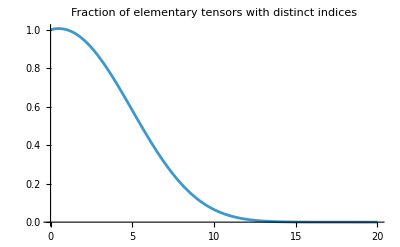

```mathematica
k=20;
Plot[(Binomial[k,d]Factorial[d])/k^d,{d,0,k},PlotRange->All,PlotLabel->"Fraction of elementary tensors with distinct indices"]
```

#### Problem For ChatGPT

Recall that

e_π_λ(H_λ^(⊗d_λ))≅⊕_(μ_λ∈Λ_Table[λ,d_λ])H_μ_λ⊗Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))).

Recall that it is easy to obtain a valid path basis {β} for VP_μ_λ^(λ,d_λ) by enumerating all valid Clebsch-Gordan paths from λ to μ_λ. Provide a combinatorial algorithm to determine whether a given basis vector β∈VP_μ_λ^(λ,d_λ) and a given Young projector e_(π_λ,μ_λ) satisfy e_(π_λ,μ_λ)(β)=0. In other words, provide a combinatorial algorithm to determine whether β∈e_(π_λ,μ_λ)(VP_μ_λ^(λ,d_λ)). The algorithm should not rely on computing many 3j or 6j coefficients; in particular, it is unsatisfactory to explicitly compute Clebsch-Gordan tensors via 3j coefficients and directly apply the Young symmetrizer, and it is unsatisfactory to apply the Young symmetrizer directly on VP_μ_λ^(λ,d_λ) by passing the symmetric group action to VP_μ_λ^(λ,d_λ) via 6j coefficients. I would like a combinatorial algorithm in terms of β and π_λ only. It is known that a single β can be smeared out over multiple isotypic components, i.e., over multiple π_λs.

#### Scratch

We know that

⊕_ν H_ν⊗VP_ν^(d+1)≅H_λ^(⊗d+1)≅⊕_μ H_μ⊗H_λ⊗VP_μ^(λ,d)≅⊕_ν H_ν⊗⊕_(|μ-ν|<=λ)VP_μ^(λ,d),

so

⊕_(|μ-ν|<=λ)VP_μ^d≅VP_ν^(d+1)

via

(λ,...,μ)↦(λ,...,μ,ν).

We know that

⊕_μ H_μ⊗VP_μ^d≅H_λ^(⊗d)≅⊕_(π⊢d)e_π(H_λ^(⊗d))⊗[π]≅⊕_(π⊢d)⊕_μ H_μ⊗e_(π,μ)(VP_μ^d)⊗[π]≅⊕_μ H_μ⊗(⊕_(π⊢d)e_(π,μ)(VP_μ^d)⊗[π]),

so

VP_μ^d≅⊕_(π⊢d)e_(π,μ)(VP_μ^d)⊗[π].

Thus,

⊕_(|μ-ν|<=λ)⊕_(π⊢d)e_(π,μ)(VP_μ^d)⊗[π]≅⊕_(π'⊢d+1)e_(π',ν)(VP_ν^(d+1))⊗[π'].

```mathematica
(*ms=
AncestralNestTree[
With[{s=Total[#],j=Length[#]},Range[Max[-λs[[j]],-γs[[j]]-s],Min[λs[[j]],γs[[j]]-s]]]&,
Tree[0,None],
Length[λs]
];

ms=Rest/@TreeData/@TreeLeaves[AncestralNestTree[{#}&,ms]];*)
```

Proposition: Define

A_R:=(ρ_j-𝟙)_j,
A_C:=(γ_k+𝟙)_k,
Fix(R_π):={v∈⊗_(j=1)^d V_j|∀σ∈R_π,σ v=v}={v∈⊗_(j=1)^d V_j|∀j,ρ_j v=v}=ker A_R
Alt(C_π):={v∈⊗_(j=1)^d V_j|∀σ∈C_π,σ v=sgn(σ)v}={v∈⊗_(j=1)^d V_j|∀k,γ_k v=-v}=ker A_C

Then r_π,c_π∈ℝ[𝔖^d] are orthogonal projections onto Fix(R_π),Alt(C_π). Moreover, e_π is a projection. To apply e_π, we need to project first onto ker A_C then onto ker A_R.

Enumerate the set {(d_λ)_(λ∈Λ_X)|d_λ∈ℕ_0,∑_(λ∈Λ_X) d_λ=D} of weak compositions of D with |Λ_X| parts using D stars and |Λ_X|-1 bars.

For each (d_λ)_λ, enumerate the set {(π_λ)_(λ∈Λ_X)|π_λ⊢d_λ,l(π_λ)<=min(dim H_λ,dim M_λ)} of tuples of partitions.

For each (d_λ)_λ, enumerate the set {(μ_λ)_(λ∈Λ_X)|μ_λ∈Λ_(λ,d_λ)} of tuples of labels.

```mathematica
Graph[{"D"->"(d_λ)_λ","(d_λ)_λ"->"(π_λ)_λ","(d_λ)_λ"->"(μ_λ)_λ","(d_λ)_λ"->"(β_λ)_λ","(d_λ)_λ"->"(α_λ)_λ","ν"->"(μ_λ)_λ","ν"->"γ","(μ_λ)_λ"->"γ","(μ_λ)_λ"->"(β_λ)_λ","(π_λ)_λ"->"(α_λ)_λ","γ"->"CG_ν^((SubscriptBox[μ, λ])_λ)","(β_λ)_λ"->"CG_((SubscriptBox[μ, λ])_λ)^((λ, SubscriptBox[d, λ])_λ)","(π_λ)_λ"->"CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ])","CG_((SubscriptBox[μ, λ])_λ)^((λ, SubscriptBox[d, λ])_λ)"->"CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ])","CG_ν^((SubscriptBox[μ, λ])_λ)"->"CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ])","CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ])"->"End","(α_λ)_λ"->"End"},VertexLabels->Placed["Name",Center],VertexSize->0.8]
```

Graph[{D->(d_λ)_λ,(d_λ)_λ->(π_λ)_λ,(d_λ)_λ->(μ_λ)_λ,(d_λ)_λ->(β_λ)_λ,(d_λ)_λ->(α_λ)_λ,ν->(μ_λ)_λ,ν->γ,(μ_λ)_λ->γ,(μ_λ)_λ->(β_λ)_λ,(π_λ)_λ->(α_λ)_λ,γ->CG_ν^((SubscriptBox[μ, λ])_λ),(β_λ)_λ->CG_((SubscriptBox[μ, λ])_λ)^((λ, SubscriptBox[d, λ])_λ),(π_λ)_λ->CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ]),CG_((SubscriptBox[μ, λ])_λ)^((λ, SubscriptBox[d, λ])_λ)->CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ]),CG_ν^((SubscriptBox[μ, λ])_λ)->CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ]),CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ])->End,(α_λ)_λ->End},VertexLabels→Placed[Name,Center],VertexSize→0.8]

Thus, since e_π is G-equivariant, we have

e_π(H_λ^(⊗d_λ))≅⊕_(μ∈Λ_(d,λ))H_μ⊗e_(π,μ)(VP_μ^(λ,d_λ))

for some linear maps e_(π,μ) on VP_μ^(λ,d_λ). Note that H_μ⊗e_(π,μ)(VP_μ^(λ,d_λ)) embeds into e_π(H_λ^(⊗d_λ)) by a Clebsch-Gordan isometry.

Theorem (Isotypic Decomposition of the Symmetric Power): Suppose that X has the isotypic decomposition

X≅⊕_λ H_λ⊗M_λ.

Then 𝒮^D(X) has the isotypic decomposition

𝒮^D(X^*)≅⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,𝒮^D(X^*)),

where

Hom_G(H_ν,𝒮^D(X^*)):=⊕_(∑_λ d_λ=D)⊕_((μ_λ∈Λ_(d,λ))_λ)Hom_G(H_ν,⊗_λ H_μ_λ)⊗⊗_λ(⊕_(π⊢d_λ)VP_μ_λ^(λ,d_λ)⊗e_π(M_λ^(⊗d_λ))).

Lemma (Basis for VP_ν^((μ_λ)_λ)): For any (μ_λ∈Λ_(d,λ))_(λ∈Λ_X) and ν∈Λ_X, the vector space VP_ν^((μ_λ)_λ) has basis given by all paths in indexPaths.

J_1:=(  |   |  
  |   | -ⅈ
  | ⅈ |  ),J_2:=(  |   | ⅈ
  |   |  
-ⅈ |   |  ),J_3:=(  | -ⅈ |  
ⅈ |   |  
  |   |  ),J_±:=1/(√2)(J_1±ⅈ J_2)=1/(√2)(  |   | ∓1
  |   | -ⅈ
±1 | ⅈ |  ).

Proposition: Depth[ℐ(a_1,...,a_d)]=Depth[a_1]+...+Depth[a_d].

Theorem (Isotypic Decomposition): X has the isotypic decomposition

X≅⊕_λ H_λ⊗M_λ,

where Λ_X:={λ∈Λ|M_λ!=0}⊆Λ is finite and

M_λ:=(H_λ^*⊗X)^G≅Hom_G(H_λ,X).

Definition: Let

A:=⊕_(Y irrep of G)(𝒮(X^*)⊗Y)^G

be the covariant algebra of X.

Remark: For certain specific X, Sahil has obtained (non-minimal) generating sets for A as an ℝ-algebra. These generating sets can be cut down to generating sets for M as an R-module, but the process is computationally expensive.

Definition:  The tensor algebra on V is the graded ℝ-algebra

𝒯(V):=⊕_(d∈ℕ_0)𝒯^d(V),
𝒯^d(V):=V^(⊗d).

The symmetrization map on 𝒯(V) is the linear map

Sym:𝒯(V)->𝒯(V),
v_1⊗…⊗v_d↦1/(d!)∑_(σ∈Σ_d) v_(σ(1))⊗…⊗v_(σ(d)).

The symmetric algebra on V is the commutative graded ℝ-algebra

𝒮(V):=Sym(𝒯(V))=⊕_(d∈ℕ_0)𝒮^d(V),
𝒮^d(V):=Sym(𝒯^d(V)),

with multiplication given by the shuffle product

⊙:𝒮(V)×𝒮(V)->𝒮(V),
(a,b)↦a⊙b:=Sym(a⊗b).

Lemma: Let G act linearly on vector spaces V,{V_α}_α. Then

g∈G acts on φ∈V^* by g φ:=φ∘g^-1,

g∈G acts on ⊕_α v_α∈⊕_α V_α by g⊕_α v_α:=⊕_α g v_α, and

g∈G acts on ⊗_α v_α∈⊗_α V_α by g⊗_α v_α:=⊗_α g v_α provided that the tensor product over α is finite.

Moreover, with respect to the above actions, there exist equivariant isomorphisms (which necessarily have equivariant inverses)

(⊕_α V_α)⊗V≅⊕_α(V_α⊗V) and

(⊕_α V_α)^*≅⊕_α V_α^* provided that the sum over α is finite.

Lemma: Let V,M be representations of G.

If M is fixed by G, then (V⊗M)^G=V^G⊗M.

Hom(V,M)≅(V^*⊗M)^G.

Lemma (Schur): Let V,W be irreducible representations of G, and let φ∈Hom(V,W). Then φ=0 or φ is an isomorphism. In particular, either Hom(V,W)=0 or Hom(V,W)≅ℂ.

Remark: To motivate the definition of 𝒮(X^*)⊗Y, consider the pairing (𝒮(X^*)⊗Y)×X->Y defined on elementary tensors (which correspond to the component functions of the polynomial) by

(φ⊗y,x)↦(φ⊗y)(x):=φ(x)y

and extended linearly to 𝒮(X^*)⊗Y, where φ(x) is defined by writing

φ=⊕_(d=0)^D⊕_(j_1,...,j_d=1)^(dim X^*)φ_(j_1... j_d)e_j_1^*⊗…⊗e_j_d^*

in terms of a basis {e_j^*}_(j=1)^(dim X^*) for X^* and declaring that

φ(x):=⊕_(d=0)^D⊕_(j_1,...,j_d=1)^(dim X^*)φ_(j_1... j_d)e_j_1^*(x)*…*e_j_d^*(x).

Note that φ(x) is a degree D polynomial in the entries of X selected by the e_j^*.

To motivate the definition of (𝒮(X^*)⊗Y)^G, fix g∈G, ∑_i φ_i⊗y_i∈𝒮(X^*)⊗Y, and x∈X. Observe that

(∑_i φ_i⊗y_i)(g x)=g((∑_i φ_i⊗y_i)(x))
⟺∑_i φ_i(g x)y_i=g(∑_i φ_i(x)y_i)
⟺∑_i (g^-1 φ_i)(x)y_i=∑_i φ_i(x)g y_i
⟺(∑_i g^-1 φ_i⊗y_i)(x)=(∑_i φ_i⊗g y_i)(x).

Thus, we conclude that ∑_i φ_i⊗y_i is equivariant iff g∑_i φ_i⊗y_i=∑_i φ_i⊗y_i for all g∈G iff ∑_i φ_i⊗y_i∈(𝒮(X^*)⊗Y)^G.

Proposition: R is a graded subalgebra of 𝒮(X^*). If conditions, then M is a finitely generated graded R-module.

Proof: First, note that

R:=(𝒮(X^*))^G=⊕_(d∈ℕ_0)(𝒮^d(X^*))^G.

Thus, R is a graded subspace of S(X^*). Moreover, since the tensor product and the symmetrization map are equivariant, the shuffle product is equivariant, so R is closed under multiplication, and moreover the multiplication respects the grading.

Next, define the scalar multiplication

R×M->M
(r,φ⊗y)↦(r⊙φ)⊗y

on elementary tensors in M, and extend the multiplication linearly to all of M. Since the shuffle product is equivariant, the scalar multiplication is well defined. That M is a graded R-module follows easily. That M is finitely generated follows from conditions.

Theorem (Maps Between Isotypic Components): Let X,Y be representations with isotypic decompositions

X≅⊕_(λ∈Λ)H_λ⊗M_λ,
Y≅⊕_(λ∈Λ)H_λ⊗N_λ.

Then for any π,λ∈Λ,

Hom(H_λ⊗M_λ,H_π⊗N_λ)≅δ_(λ π)Hom(M_λ,N_π).

Moreover, the R-module multiplication

R⊗M->M

corresponds to the multiplication

N_(0,d)⊗N_(ρ,e)->N_(ρ,d+e),
n_(0,d)⊗n_(ρ,e)↦SOMETHING

on each graded piece in the isotypic decomposition.

Definition: Given λ_1,...,λ_d∈Λ, define T_(λ_1,...,λ_d) be the corresponding left associate binary tree defined recursively as follows:

there are d leaf nodes containing the data λ_1,...,λ_d from left to right, and

each parent node with left child a_1 and right child a_2 contains the data ℐ(a_1,a_2).

Given ℛ_D,ℳ_D for all D=0,1,2,...

For D=1,2,...

For D'=1,2,...,D

For r_D'∈ℛ_D',m_(D-D')∈ℳ_(D-D'), multiply r_D' with m_(D-D') as monomials

#### Reduce to finding a basis for the subspace of monomials

Theorem 1 (https://arxiv.org/abs/2406.01552): Write X as the direct sum

X=⊕_(j=1)^J X_j

of irreducible representations X_j. There exists an equivariant isomorphism of graded ℝ-algebras

𝒮(X^*)≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=...<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*,

which restricts to an equivariant isomorphism of graded ℝ-algebras

R=(𝒮(X^*))^G≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=...<=j_d<=J)(X_j_1^*⊗…⊗X_j_d^*)^G.

There exists an equivariant isomorphism of graded ℝ-modules and graded R-modules

𝒮(X^*)⊗Y≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=...<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*⊗Y,

which restricts to an equivariant isomorphism of graded ℝ-modules and graded R-modules

M=(𝒮(X^*)⊗Y)^G≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=...<=j_d<=J)(X_j_1^*⊗…⊗X_j_d^*⊗Y)^G.

Proof: First, observe that

𝒯(X^*)=⊕_(d∈ℕ_0)𝒯^d(X^*)=⊕_(d∈ℕ_0)(X^*)^(⊗d)≅⊕_(d∈ℕ_0)(⊕_(j=1)^J X_j^*)^(⊗d)≅⊕_(d∈ℕ_0)⊕_(j_1,...,j_d=1)^J X_j_1^*⊗…⊗X_j_d^*,

where the multiplication on the right-hand side is still the ordinary tensor product. Symmetrizing yields Eq. (1),

𝒮(X^*)≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=...<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*,

where the multiplication on the right-hand side is defined by declaring the product of X_j_1^*⊗…⊗X_j_d^* and X_k_1^*⊗…⊗X_k_e^* to be X_j_1^*⊗…⊗X_j_d^*⊗X_k_1^*⊗…⊗X_k_e^* with the indices reordered to be nondecreasing.

Corollary: The monomial parts of an equivariant polynomial are equivariant.

𝒮^d_λ(H_λ⊗M_λ)=((H_λ⊗M_λ)^(⊗d_λ))^(𝔖^d_λ)≅(H_λ^(⊗d_λ)⊗M_λ^(⊗d_λ))^(𝔖^d_λ)
≅^(Schur-Weyl duality)((⊕_(π∈P(d_λ,h_λ))e_π(H_λ^(⊗d_λ))⊗[π])⊗(⊕_(π∈P(d_λ,m_λ))e_π(M_λ^(⊗d_λ))⊗[π]))^(𝔖^d_λ)
≅^(Schur Lemma)⊕_(π⊢d_λ)e_π(H_λ^(⊗d_λ))⊗e_π(M_λ^(⊗d_λ)),

#### Isotypic decomposition of the tensor product, d=2 (Clebsch–Gordan Theory)

Definition (Clebsch-Gordan Intertwiner): Let δ∈𝒮^2(V) be the Kronecker delta, and let ϵ∈𝒯^3(V) be the Levi-Civita tensor. For a,b>=1, define contraction with δ as

Tr_δ:𝒮^(a+b)(V^*)->𝒮^(a+b-2)(V^*),
f↦f(δ),

and contraction with ϵ as

Tr_ϵ:𝒮^a(V^*)⊗𝒮^b(V^*)->𝒮^(a+b-1)(V^*),
f⊗g↦Sym(ϵ_i^(j k)f_(j *)g_(k *)).

Let π_ℋ:𝒮(V^*)->ℋ(V^*) be the canonical projection. Define the maps

P_δ^k:ℋ^a(V^*)⊗ℋ^b(V^*)(->)^Sym 𝒮^(a+b)(V^*)(->)^(Tr_δ^k)𝒮^(a+b-2k)(V^*)(->)^π_ℋ ℋ^(a+b-2k)(V^*),0<=k<=min{a,b},
P_(ϵ,δ)^k:ℋ^a(V^*)⊗ℋ^b(V^*)(->)^Tr_ϵ 𝒮^(a+b-1)(V^*)(->)^(Tr_δ^k)𝒮^(a+b-1-2k)(V^*)(->)^π_ℋ ℋ^(a+b-1-2k)(V^*),0<=k<=min{a,b}-1.

Proposition: Tr_δ,Tr_ϵ,π_ℋ,P_δ^k,P_(ϵ,δ)^k are surjective equivariant linear maps. Moreover, we have dual maps

Tr_δ^*:𝒮^(a+b-2)(V)->𝒮^(a+b)(V),
A↦Sym(δ⊗A),

and

Tr_ϵ^*:𝒮^(a+b-1)(V)->𝒮^a(V^*)⊗𝒮^b(V^*),
A↦(Sym⊗Sym).

Proof: Show that P_δ^k,P_(ϵ,δ)^k are surjective equivariant linear maps.

To prove Eq. (5), define

P:=⊕_(k=0)^(min{a,b})P_δ^k⊕⊕_(k=0)^(min{a,b}-1)P_(ϵ,δ)^k,

which is a surjective equivariant linear map. Thus, since

dim(ℋ^a(V^*)⊗ℋ^b(V^*))=(2a+1)(2b+1)=dim(⊕_(k=0)^(min{a,b})Im P_δ^k⊕⊕_(k=0)^(min{a,b}-1)Im P_(ϵ,δ)^k),

P is an isomorphism.

Finally, note that

(ℋ^a(V^*)⊗ℋ^b(V^*))^G≅⊕_(k=0)^(min{a,b})(ℋ^(a+b-2k)(V^*))^G⊕⊕_(k=0)^(min{a,b}-1)(ℋ^(a+b-1-2k)(V^*))^G.

If d=0, then ℝ≅ℋ^d(V^*)=(ℋ^d(V^*))^G. If d>0, then (ℋ^d(V^*))^G=0, since any nonzero v∈(ℋ^d(V^*))^G would yield a nontrivial proper sub-representation 0<Span{v}<ℋ^d(V^*), as dim ℋ^d(V^*)=2D+1>1.

Given: D,Λ_X,M_λ

Define n=|Λ_X|

Enumerate {∑_(λ∈Λ_X) d_λ=D|(‖d‖)_1=D}

Define m=|Λ_(d,λ)|=1+max_(λ∈Λ_X) λ d_λ

Enumerate {(μ_λ∈Λ_(d,λ))_(λ∈Λ_X)} using n-digit m-ary numbers in lexicographic (i.e., increasing) order (should be m^n terms)

Apply Clebsch-Gordan on ⊗_(λ∈Λ_X)H_μ_λ to determine C_0^μ and C_ρ^μ

For each λ∈Λ_X and each partition π of d_λ with

## Draft Stuff (Old)

DRAFT STUFF: Towards this, note that Sym^d is equivariant, and Tr^d is equivariant provided that G is a subgroup of O(V).

𝒯^d(V)(->)^(Sym^d)𝒮^d(V)(->)^(Tr^d)𝒮^(d-2)(V)
ℋ^d(V):=Im Sym^d∩Ker Tr^d

(𝒯^d(V))^G(->)^(Sym_G^d)(𝒮^d(V))^G(->)^(Tr_G^d)(𝒮^(d-2)(V))^G
(ℋ^d(V))^G=(Im Sym^d)^G∩(Ker Tr^d)^G=Im Sym_G^d∩Ker Tr_G^d

Suppose we have a basis ℬ for (𝒯^d(V))^G. Then Sym_G^d(ℬ) generates (𝒮^d(V))^G. Standard linear algebra can cut down provided that ℬ doesn’t have too many elements. For our use case (d=11), I expect linear systems on the order of 10^4×10^4. Not great but also not terrible.

TODO: First get basis for SO(V) and T(V). Then see if you can shortcut to automatically identify a natural basis for S(V). Count dimensions if needed. Similarly, see if you can shortcut to get a natural basis for H(V). Again count dimensions. Worst case we do the brute force solution above. Best case this method works.

#### Find a basis for (ℋ^λ(V))^(SO(3))

Definition: Let 𝒫_(O(V))(m) denote the set of perfect matchings of {1,...,m}. For any P={{i_1,j_1},...,{i_l,j_l}}∈𝒫_(O(V))(m), define σ_P∈S_(2l) to be the permutation whose two-line notation is

σ_P:=(1 | 2 | … | 2l-1 | 2l
i_1 | j_1 | … | i_l | j_l),

where the second row is ordered such that i_m<j_m for all m∈{1,...,l} and i_m<i_(m+1) for all m∈{1,...,l-1}. Further define T_P∈𝒯^m(V) to be the tensor

T_P:=σ_P((⊕_(i,j=1)^(dim V)δ_(i j)e_i⊗e_j)^(⊗l)).

Lemma 2: The set

{T_P}_(P∈𝒫_(O(V))(m))

is a basis for (𝒯^m(V))^(O(V)) of size ((2l)!)/(2^l l!).

Definition: Let 𝒫_(SO(V))(m) denote the set of non-crossing planar partitions of {1,...,m} with no singletons. For any P={B_1,...,B_j}∈𝒫_(SO(V))(m), define

T_P:=

Lemma 3: The set

{T_P}_(P∈𝒫_(SO(V))(m))

is a basis for (𝒯^m(V))^(SO(V)) of size [m^th Riordan number].

#### Find a basis for the subspace of monomials

Remark 6: Problem 3 has been solved for X_j=𝒯^d_j(V), Y=𝒯^d(V), and G=O(V) in https://arxiv.org/abs/2406.01552. I think Problem 3 has also been solved for X_j=𝒯^d_j(V), Y=𝒯^d(V), and G=SO(V).

Remark 7: For the turbulence application, we must solve Problem 3 for X_j=ℋ^d_j(V), Y=ℋ^d(V), and G=SO(V). That is, we have to find bases for

the space of monomial SO(3)-invariant polynomial maps from harmonic tensors to ℝ

the space of monomial SO(3)-equivariant polynomial maps from harmonic tensors to harmonic tensors

I’m not actually sure that this is so easy.

Remark 8: Appendix A in https://arxiv.org/pdf/2404.18735 shows that any invariant polynomial 𝒮^d(V)->ℝ is the restriction of an invariant polynomial 𝒯^d(V)->ℝ (however, there are polynomial extensions that are not invariant). Results like this might help.

Remark 5: We might want to investigate conditions under which the fixed set of the tensor product is the tensor product of the fixed sets (this is not true in general). This would simplify the theory and reduce the computational complexity dramatically. This would also allow for arbitrary combinations of tensors/symmetric tensors/harmonic tensors in X and Y.

For turbulence modeling, we care about the following special case.

2,2,3,4, so k=11 what

In particular, we have

ℐ(a_1,...,a_d,b_1,...,b_e)=ℐ(ℐ(a_1,...,a_d),ℐ(b_1,...,b_e)).

## Approach via Invariant Scalar Functions (Old)

The relevant module and algebra both live in a large parent module:

N | := | Invariant(⊕_j Ker(tr^n_j)⊕(V^*)^(⊗n),ℝ) | module over R
| |   | | |  
M | := | Equivariant(⊕_j Ker(tr^n_j),Sym(V^(⊗n))) | module over R
| |   | | |  
R | := | Invariant(⊕_j Ker(tr^n_j),ℝ) | algebra over ℝ

where M is embedded in N via m↦m(·)·. To obtain a minimal generating set for M, one strategy is to obtain a minimal generating set for the isomorphic copy of M in N, which consists of invariant, scalar-valued functions that are multilinear and symmetric in the components of the second argument.

$Aborted